# Graph states on Rydberg neutral atoms

main ref : www.nature.com/articles/s41586-022-04592-6

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink. Now it works as well directly using the default pre-compiled binary. But it usea only single core.

```mathematica
Import["~/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz
Length unit: μm

## 1D cluster state

```mathematica
el=Join[#<->#+1->1&/@Range[0,10,2],#<->#+1->2&/@Range[1,9,2]];
cluster=Graph[el//Keys,VertexSize->0.5,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{17,FontFamily->"Serif"},ImageSize->900,EdgeStyle->Directive[Black,Thick],VertexLabels->Placed[Automatic,Center],EdgeLabels->el,EdgeLabelStyle->Directive[Background->White,Bold,Red]]
```

-Graphics-

-Graphics-

```mathematica
cs1dmean={0.8814814814814814,0.8314814814814814,0.8888888888888887,0.8629629629629629,0.8814814814814814,0.8796296296296295,0.8555555555555554,0.8759259259259258,0.8722222222222221,0.8777777777777775,0.8462962962962962,0.8925925925925925}
cs1dminus={0.8537037037037036,0.8018518518518518,0.8629629629629629,0.8333333333333333,0.8537037037037036,0.8537037037037036,0.8277777777777777,0.8481481481481481,0.8444444444444444,0.8481481481481481,0.8185185185185184,0.8685185185185184};
cs1dplus={0.9018518518518518,0.8574074074074074,0.912962962962963,0.8870370370370371,0.9037037037037035,0.9037037037037035,0.8814814814814814,0.898148148148148,0.8962962962962961,0.898148148148148,0.8722222222222221,0.9148148148148149};
```

{0.881481,0.831481,0.888889,0.862963,0.881481,0.87963,0.855556,0.875926,0.872222,0.877778,0.846296,0.892593}

```mathematica
cs1d=Around[#[[1]],#[[2;;]]-#[[1]]]&/@Transpose[{cs1dmean,cs1dminus,cs1dplus}]
```

{0.8810.0280.020,0.8310.0300.026,0.8890.0260.024,0.8630.0300.024,0.8810.0280.022,0.8800.0260.024,0.8560.0280.026,0.8760.0280.022,0.8720.0280.024,0.8780.0300.020,0.8460.0280.026,0.8930.0240.022}

```mathematica
Mean@cs1d
```

0.8710.0080.007

```mathematica
(* Expected value of each stabiliser S_j *)
stabcluster={0.8772585669781932,0.8274143302180685,0.887227414330218,0.8598130841121496,0.8772585669781932,0.8772585669781932,0.852336448598131,0.8722741433021808,0.8697819314641745,0.8722741433021808,0.8423676012461061,0.8897196261682243};
(* <S_j> on the noisy one *)
meancluster=0.87;
(*  <S_j> on ideal SPAM *)
sideal=0.91;
```

## The virtual device specification

```mathematica
Options[RydbergHub]={
(* The total number of physical qubits *)
QubitNum-> 12,
(*Physical location on each qubit described with 2D-vector*)
AtomLocations-><|#->{#,0}&/@VertexList@cluster|>,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.5*10^6,
(* vacuum life time, where T1=τvac/N in μs *)
VacLifeTime->48*10^6,
(* Rabi frequency MHz *)
RabiFreq->1,
(* Asymmetric Bit-flip probability during single qubit operation *)
ProbBFRot-><|10->0.02, 01->0.03|>,
(* Unit lattice in μm. This will be the unit of the lattice/locations given in qubitLocations *)
UnitLattice->3,
(* blockade radius in μm*)
BlockadeRadius->1,
(* Leakage probability in the initalisation *)
ProbLeakInit->0.001,
(* Duration of moving atoms *)
DurMove->0.01,
(* duration on the initialization which involves the atom loading (~50%) and rearranging the tweezer *)
DurInit->5*10^5,
(* measurement induces atom loss afterward *)
FidMeas-> 0.98,
DurMeas-> 10,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas-> 0.01,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ-> <|01-> 0.006,11->0.001 |>
};
```

## Drawing

```mathematica
(*returns graph state stabilizer of a node*)
stabgs[graph_,node_]:=With[{neig=Complement[VertexList@NeighborhoodGraph[graph,node],{node}]},
ToExpression[StringRiffle[Join[{Subscript[X, node]},Subscript[Z, #]&/@neig]]]]
```

```mathematica
showgs[title_:"",opt_:{}]:=PlotAtoms[devGS,Sequence@@opt,ImageSize->900,ShowBlockade->Range[0,11],LabelStyle->Directive[17,Black],BaseStyle->{16,FontFamily->"Times"},PlotRange->{{-1,37},{-1.3,1.3}},Epilog->Inset[Style[title,{Red,Bold}],Scaled[{0.97,0.15}]],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],
FrameTicks->{{{-1,0,1},Automatic},{Automatic,Automatic}}
];
```

```mathematica
circ1=CircRydbergHub[Flatten@{{Subscript[Init, #],Subscript[Ry, #][π/2]}&/@Range[0,11]},RydbergHub[],Parallel->True];
circ2={{Subscript[ShiftLoc, Range[1,11,2]][{-0.75,0}]}};
circ3={Subscript[C, #][Subscript[Z, #+1]]&/@Range[0,10,2]};
circ4={{Subscript[ShiftLoc, Range[1,11,2]][{1.5,0}]}};
circ5={Subscript[C, #][Subscript[Z, #+1]]&/@Range[1,9,2]};
```

```mathematica
devGS=RydbergHub[];
f1=showgs["initial",{ImagePadding->{{30,20},{0,0}}}];
noisycirc1=InsertCircuitNoise[circ1,devGS];
noisycirc2=InsertCircuitNoise[circ2,devGS];
f2=showgs["       1",{ImagePadding->{{30,20},{0,0}}}];
noisycirc3=InsertCircuitNoise[circ3,devGS];
noisycirc4=InsertCircuitNoise[circ4,devGS];
f3=showgs["       2",{ImagePadding->{{30,20},{20,0}}}];
noisycirc5=InsertCircuitNoise[circ5,devGS];
```

```mathematica
Column[{cluster,f1,f2,f3},Center,Spacings->0]
Export["~/vqd/img/rydberg_graph.pdf",%]
```

-Graphics-

~/vqd/img/rydberg_graph.pdf

## Setups

```mathematica
DestroyAllQuregs[];
ρ=CreateDensityQureg[12];
ρinit=CreateDensityQureg[12];
ρwork=CreateDensityQureg[12];
ρstore=CreateDensityQureg[12];
```

```mathematica
SetQuregMatrix[ρinit,RandomMixState[12]];
```

```mathematica
totalcirc=Join@@(ToExpression["circ"<>ToString@#]&/@Range[1,5])
```

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8,Init_9,Init_10,Init_11},{Ry_0[π/2],Ry_1[π/2],Ry_2[π/2],Ry_3[π/2],Ry_4[π/2],Ry_5[π/2],Ry_6[π/2],Ry_7[π/2],Ry_8[π/2],Ry_9[π/2],Ry_10[π/2],Ry_11[π/2]},{ShiftLoc_{1,3,5,7,9,11}[{-0.75,0}]},{C_0[Z_1],C_2[Z_3],C_4[Z_5],C_6[Z_7],C_8[Z_9],C_10[Z_11]},{ShiftLoc_{1,3,5,7,9,11}[{1.5,0}]},{C_1[Z_2],C_3[Z_4],C_5[Z_6],C_7[Z_8],C_9[Z_10]}}

```mathematica
noisycirc=InsertCircuitNoise[totalcirc,RydbergHub[]];
(*Simplify, remove errors with zero-parameters *)
enoisycirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.]}];
```

Run the circuit without measurement. We start from an unknown mixed state

```mathematica
ApplyCircuit[CloneQureg[ρ,ρinit],enoisycirc]
```

{}

### [Quoted values] SPAM removal: 0.91, noisy: 0.87

#### Pulled from the density matrix

```mathematica
stabdata=CalcExpecPauliString[ρ,stabgs[cluster,#],ρwork]&/@Range[0,11]
Mean@stabdata
```

{0.91502,0.915066,0.915034,0.915069,0.915034,0.915069,0.915034,0.915069,0.915034,0.915069,0.915031,0.915059}

0.915049

#### Gather the statistics by shots

Note that the “X” measurement done in the circuit is flipped: H=Ry[π/2]X

```mathematica
CalcCircuitMatrix[{Subscript[Ry, 0][π/2],Subscript[X, 0]}]//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
DrawCircuit@{Subscript[Ry, 0][π/2],Subscript[X, 0]}
```

-Graphics-

```mathematica
CalcCircuitMatrix[Subscript[X, 0]].CalcCircuitMatrix[Subscript[Ry, 0][π/2]]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

### The graph state simulation

```mathematica
(*Two measurement settings: {Subscript[S, j]} where (1) j are even, (2) j are odd  
Put measurements at the very last!*)
evensm={Subscript[Ry, #][π/2]&/@Range[0,11,2],Subscript[M, #]&/@Range[0,11]};
oddsm={Subscript[Ry, #][π/2]&/@Range[1,11,2],Subscript[M, #]&/@Range[0,11]};
```

```mathematica
ClearAll[SimulateGraphState]
SimulateGraphState[ρ_,ρinit_,ρwork_,ρstore_,nshots_,options_:{}]:=Module[{noisycirc,enoisycirc,emeasnoisy,omeasnoisy,statevenmeas={},statoddmeas={},scount,outeig,stabideal,totalcirc,chart,mean,ideal,cluster},
totalcirc={
{Subscript[Init, 0],Subscript[Init, 1],Subscript[Init, 2],Subscript[Init, 3],Subscript[Init, 4],Subscript[Init, 5],Subscript[Init, 6],Subscript[Init, 7],Subscript[Init, 8],Subscript[Init, 9],Subscript[Init, 10],Subscript[Init, 11]},{Subscript[Ry, 0][π/2],Subscript[Ry, 1][π/2],Subscript[Ry, 2][π/2],Subscript[Ry, 3][π/2],Subscript[Ry, 4][π/2],Subscript[Ry, 5][π/2],Subscript[Ry, 6][π/2],Subscript[Ry, 7][π/2],Subscript[Ry, 8][π/2],Subscript[Ry, 9][π/2],Subscript[Ry, 10][π/2],Subscript[Ry, 11][π/2]},{Subscript[ShiftLoc, {1,3,5,7,9,11}][{-0.75,0}]},{Subscript[C, 0][Subscript[Z, 1]],Subscript[C, 2][Subscript[Z, 3]],Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 6][Subscript[Z, 7]],Subscript[C, 8][Subscript[Z, 9]],Subscript[C, 10][Subscript[Z, 11]]},{Subscript[ShiftLoc, {1,3,5,7,9,11}][{1.5,0}]},{Subscript[C, 1][Subscript[Z, 2]],Subscript[C, 3][Subscript[Z, 4]],Subscript[C, 5][Subscript[Z, 6]],Subscript[C, 7][Subscript[Z, 8]],Subscript[C, 9][Subscript[Z, 10]]}
};
cluster=Keys@Join[#<->#+1->1&/@Range[0,10,2],#<->#+1->2&/@Range[1,9,2]];
noisycirc=InsertCircuitNoise[totalcirc,RydbergHub[Sequence@@options]];
(*Simplify, remove errors with zero-parameters *)
     enoisycirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.]}];
ApplyCircuit[CloneQureg[ρ,ρinit],enoisycirc];
CloneQureg[ρstore,ρ];
emeasnoisy=ExtractCircuit@InsertCircuitNoise[evensm,RydbergHub[Sequence@@options]];
omeasnoisy=ExtractCircuit@InsertCircuitNoise[oddsm,RydbergHub[Sequence@@options]];

Table[
(* Note that this is okay because we don't have any function that depends on the absolute time.*)
(* even measurements*)
CloneQureg[ρ,ρstore];
AppendTo[statevenmeas,Flatten@ApplyCircuit[ρ,emeasnoisy]];
(* odd measurements*)
CloneQureg[ρ,ρstore];
AppendTo[statoddmeas,Flatten@ApplyCircuit[ρ,omeasnoisy]];
,{nshots}
];

(* stabilizer count *)
scount=Association@Table[j->0,{j,VertexList@cluster}];
(* First measurement setting: X,Z,X,Z...*)
Table[
outeig=Table[
If[EvenQ[k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];
Table[
(* +1 - -1 *)
scount[node]+=Times@@(outeig[[#+1]]&/@VertexList[NeighborhoodGraph[cluster,node]]);
,{node,0,11,2}];
,{out,statevenmeas}];
(* Second measurement setting: Z,X,Z,X...*)
Table[
outeig=Table[
If[OddQ[k-1],
out[[k]]/.{0:>-1}, (*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];
Table[
scount[node]+=Times@@(outeig[[#+1]]&/@VertexList[NeighborhoodGraph[cluster,node]]);
,{node,1,11,2}];
,{out,statoddmeas}];
stabideal=CalcExpecPauliString[CloneQureg[ρ,ρstore],stabgs[cluster,#],ρwork]&/@Range[0,11];
mean=N@Mean@Values[scount/nshots];
ideal=Mean[stabideal];
<|"opt"->RydbergHub[Sequence@@options][OptionsUsed],"outeven"->statevenmeas,"outodd"->statoddmeas,"scount"->scount,"sideal"->stabideal|>
]
```

```mathematica
drawChart[res_,expresults_]:=With[{scount=res["scount"],nshots=res["outeven"]//Length,stabideal=res["sideal"]},
Show[
BarChart[Values@scount/nshots,ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,11]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->1.2,ChartStyle->ColorData["DeepSeaColors"][0.7],PlotRange->{Automatic,{-0.05,1}}],
BarChart[expresults,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]],
ListPlot[stabideal,Joined->True,PlotMarkers->{"■",15},PlotStyle->RGBColor[0.6913629326773305, 0.22460288235842985, 0.347286180798712]],ImageSize->{Automatic,400},Background->White,LabelStyle->{16,FontFamily->"Serif"},
ImagePadding->{{30,0},{30,10}}
]
]

showResults[res_,expresults_]:=With[{dev=RydbergHub[Sequence@@res[["opt"]]],nshots=res["outeven"]//Length},
<|"nshots"->ToString@nshots,"chart"->drawChart[res,expresults],"erravg"->Mean@Abs[N[Values@cluster1d[[11]][["scount"]]/nshots]-expresults],
"errmax"->Max@Abs[N[Values@cluster1d[[11]][["scount"]]/nshots]-expresults],
"stabavg"->N@Mean@Values@res[["scount"]]/nshots,
"nospamavg"->Mean@res[["sideal"]]|>
]
```

The best result on the cluster

```mathematica
cluster1d<<cluster1d.mx;
```

```mathematica
cluster1d[[11]][["opt"]]
```

{qubitsNum→12,AtomLocations→<|0→{0,0},1→{1,0},2→{2,0},3→{3,0},4→{4,0},5→{5,0},6→{6,0},7→{7,0},8→{8,0},9→{9,0},10→{10,0},11→{11,0}|>,T2→1.5×10^6,VacLifeTime→48000000,RabiFreq→1,ProbBFRot→<|10→0.02,1→0.03|>,UnitLattice→3,BlockadeRadius→1,ProbLeakInit→0.001,ProbLeakMove→0.01,DurInit→500000,FidMeas→0.977,DurMeas→10,ProbLossMeas→0.01,ProbLeakCZ→<|1→0.006,11→0.001|>}

```mathematica
res=SimulateGraphState[ρ,ρinit,ρwork,ρstore,10000,cluster1d[[11]][["opt"]]];
AppendTo[cluster1d,res];
showResults[cluster1d[[-1]],cs1d]
```

OptionValue::nodef: Unknown option ProbLeakMove for RydbergHub.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

ApplyCircuit::error: Calculation aborted. The qureg (id 0) has been restored to its prior state.

$Aborted

Part::pspec1: Part specification opt is not applicable.

Values::invrl: The argument res[scount] is not a valid Association or a list of rules.

$Aborted

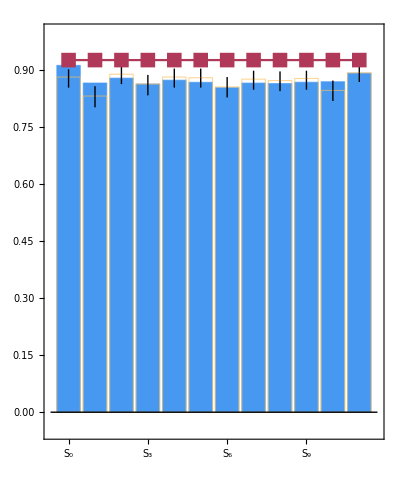
<|nshots→10000,chart→-Graphics-,erravg→0.0130.0080.007,errmax→Max[0.0000.0300.024,0.0000.0240.022,0.0020.0280.026,0.0080.0280.024,0.0080.0280.022,0.0100.0300.020,0.0100.0260.024,0.0100.0280.022,0.0120.0260.024,0.0230.0280.026,0.0310.0280.020,0.0340.0300.026],stabavg→0.872717,nospamavg→0.926101|>

~/vqd/img/stab_gs.pdf

```mathematica
showResults[cluster1d[[11]],cs1d]
Export["~/vqd/img/stab_gs.pdf",%["chart"]]
```

## Steane code

## Device configuration

```mathematica
stlocs=<|6->{0,1},5->{1,1},2->{2,1},1->{4,1},4->{2,0},0->{4,0},3->{5,0}|>;
Options[RydbergHub]={
qubitsNum-> 7,
AtomLocations->stlocs,
T2->1.5*10^6,
VacLifeTime->48*10^6,
RabiFreq->1,
ProbBFRot-><|10->0.02, 01->0.03|>,
ProbLeakMove->0.01,
UnitLattice->3,
BlockadeRadius->1,
ProbLeakInit->0.001,
DurInit->5*10^5,
FidMeas-> 0.977,
DurMeas-> 10,
ProbLossMeas-> 0.01,
ProbLeakCZ-><|01->0.006,11->0.001|>
};
```

## Experimental results

-Graphics-

```mathematica
steanemean={0.5246212121212122,0.4924242424242424,0.5170454545454546,0.7329545454545454,0.7045454545454546,0.7462121212121211};
steaneminus={0.5,0.46780303030303033,0.4905303030303031,0.7121212121212122,0.6799242424242425,0.7234848484848485};
steaneplus={0.5454545454545455,0.5151515151515151,0.5378787878787878,0.7518939393939393,0.7234848484848485,0.7651515151515151};
```

```mathematica
lsteanemean={0.7134502923976608,-0.015594541910331362};
lsteaneminus={0.6939571150097467,-0.050682261208577};
lsteaneplus={0.7290448343079922,0.009746588693957212};
```

```mathematica
steane=Partition[Around[#[[1]],#[[2;;]]-#[[1]]]&/@Transpose[{steanemean,steaneminus,steaneplus}],3]
lsteane=Around[#[[1]],#[[2;;]]-#[[1]]]&/@Transpose[{lsteanemean,lsteaneminus,lsteaneplus}]
```

{{0.5250.0250.021,0.4920.0250.023,0.5170.0270.021},{0.7330.0210.019,0.7050.0250.019,0.7460.0230.019}}

{0.7130.0190.016,-0.0160.0350.025}

```mathematica
(*stabsteane={{0.52,0.49,0.51},{0.732,0.7,0.75}};*)
logsteane={0.71,-0.02};
cols={RGBColor[0.3881893059227455, 0.5310037952810274, 0.49489914553171],RGBColor[0.93, 0.6, 0.15]};
```

```mathematica
steaneCharts[res_,expstabs_,explogic_]:=With[
{sxcount=res["sxcount"],szcount=res["szcount"],nshots=Length@res["outx"],sxideal=res["sxideal"],szideal=res["szideal"],logiccount=res["logiccount"],logicideal=res["logicideal"]},
Row@{
Show[
BarChart[
Flatten@{Values@sxcount/nshots,Values@szcount/nshots},ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,5]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->2.5,ChartStyle->Flatten@{ConstantArray[cols[[1]],3],ConstantArray[cols[[2]],3]},
PlotRange->{Automatic,{-0.05,1}},Background->White,ImageSize->{Automatic,400},ImagePadding->{{30,0},{30,10}},BaseStyle->{16,FontFamily->"Serif"}],
ListPlot[{Join[sxideal,szideal],Join[sxideal,szideal]},Joined->True,PlotMarkers->{"■",15},PlotStyle->RGBColor[0.6913629326773305, 0.22460288235842985, 0.347286180798712]],
BarChart[Flatten@expstabs,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]]
],
Show[
BarChart[Values@logiccount/nshots,ChartLabels->{"X_L","Z_L"},Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->5,ChartStyle->cols,PlotRange->{{0.,3},{-0.05,1}},FrameTicks->{Automatic,Automatic},BaseStyle->{16,FontFamily->"Serif"}],
BarChart[explogic,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]],
Background->White,ImageSize->{Automatic,400},ImagePadding->{{0,0},{30,10}}
]
}
]
steaneResults[res_,expstabs_,explogic_]:=With[{dev=RydbergHub[Sequence@@res[["opt"]]],nshots=res["outx"]//Length},
<|
"nshots"->nshots,
"charts"->steaneCharts[res,expstabs,explogic],
"avgstab"-><|"x"->N@Mean@Values@res["sxcount"]/nshots,"z"->N@Mean@Values@res["szcount"]/nshots,"xl"->N[res["logiccount"]["x"]/nshots],"zl"->N[res["logiccount"]["z"]/nshots]|>,
"errmaxstab"-><|"x"->N@Max@Abs[res["sxcount"]/nshots-First@expstabs],"z"->N@Max@Abs[res["szcount"]/nshots-Last@expstabs]|>,
"erravgstab"-><|"x"->N@Mean@Abs[Values@res["sxcount"]/nshots-First@expstabs],"z"->N@Mean@Abs[Values@res["szcount"]/nshots-Last@expstabs]|>,
"errlogic"-><|"x"->Abs[res["logiccount"]["x"]/nshots-First@explogic],"z"->Abs[res["logiccount"]["z"]/nshots-Last@explogic]|>,
"idealavg"-><|"x"->Mean@res["sxideal"],"z"->Mean@res["szideal"],"xl"->res["logicideal"]["x"],"zl"->res["logicideal"]["z"]|>
|>
]
```

```mathematica
steane7//Length
```

1063

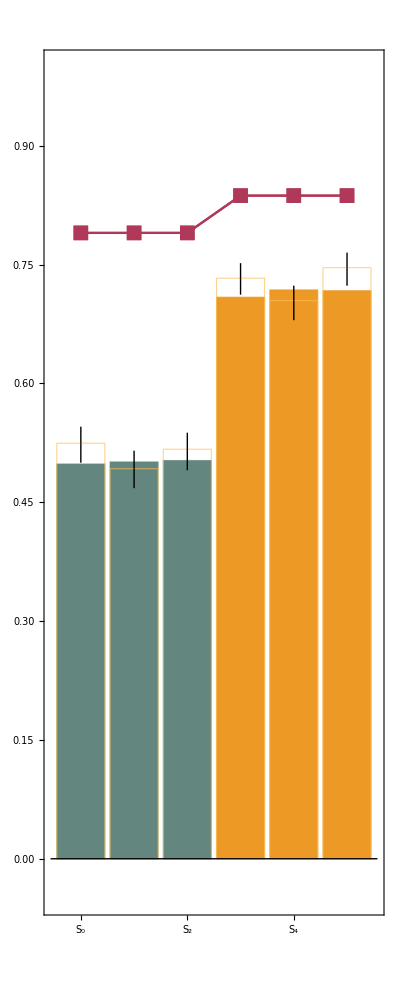
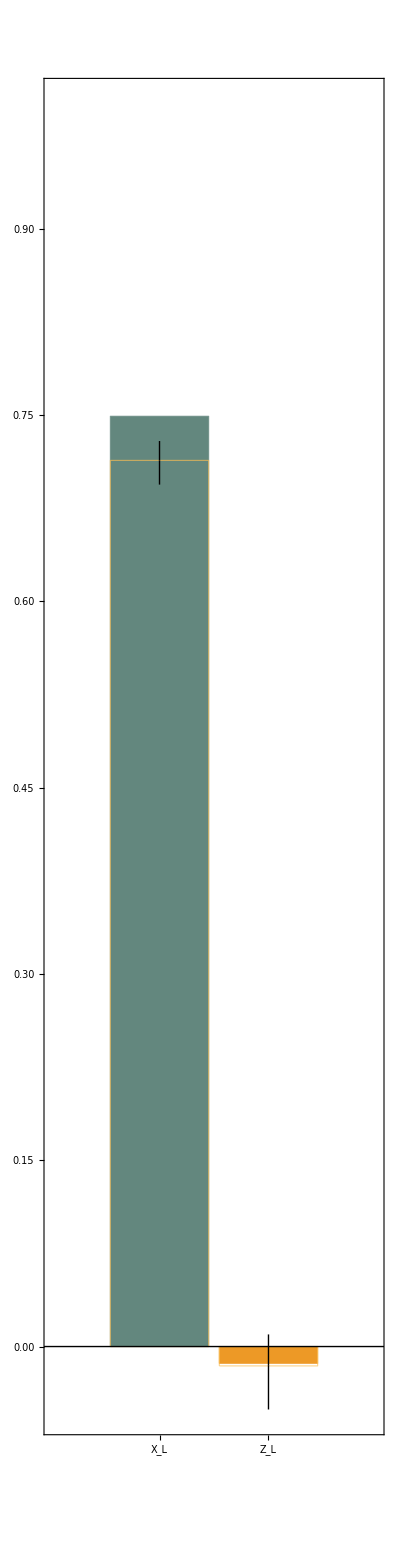

~/vqd/img/stab_steane.pdf

```mathematica
steaneCharts[steane7[[1008]],steane,lsteane]
Export["~/vqd/img/stab_steane.pdf",%]
```

```mathematica
stabx={Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 6],Subscript[X, 2] Subscript[X, 4] Subscript[X, 5] Subscript[X, 6],Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 5]};
stabz={Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 6],Subscript[Z, 2] Subscript[Z, 4] Subscript[Z, 5] Subscript[Z, 6],Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 3] Subscript[Z, 5]};
xlogic=Subscript[X, 0] Subscript[X, 1] Subscript[X, 3];
zlogic=Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 3];
(* returns indices of the involved stabilizers *)
stabindex[stab_]:=Level[stab,1]/.Subscript[_,j_]:>j 

SimulateSteane[ρ_,ρinit_,ρwork_,ρstore_,nshots_,options_:{}]:=Module[{xmeascirc,zmeascirc,circ0,circ1,circ2,circ3,circ4,circ5,stabx,stabz,stabxid,stabzid,xlogic,zlogic,steanecirc,measz={},measx={},hposz,hposx,outeig,sxcount,szcount,meas,sign,zidx,sxideal,szideal,logiccount,logic,res},

(*hadamard positions in implementing measurements*)
hposz={0,3,4};
hposx={1,2,5,6};

circ0={Subscript[Init, #]&/@Range[0,6],Subscript[Ry, #][π/2]&/@Range[0,6]};
circ1={{Subscript[ShiftLoc, 4,0,3][{-0.2,0.8}]},{Subscript[C, 2][Subscript[Z, 4]],Subscript[C, 0][Subscript[Z, 1]]}};
circ2={{Subscript[ShiftLoc, 2][{1,0}],Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 2][Subscript[Z, 0]],Subscript[C, 1][Subscript[Z, 3]]}};
circ3={{Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 6]],Subscript[C, 2][Subscript[Z, 3]]}};
circ4={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]}};
meas=Subscript[M, #]&/@Range[0,6];
steanecirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4],RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
zmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposz,meas},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
xmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposx,meas},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
(*x and z stabilizer *)
stabx={Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 6],Subscript[X, 2] Subscript[X, 4] Subscript[X, 5] Subscript[X, 6],Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 5]};
stabz={Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 6],Subscript[Z, 2] Subscript[Z, 4] Subscript[Z, 5] Subscript[Z, 6],Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 3] Subscript[Z, 5]};
(* logical pauli-x and pauli-z *)
xlogic=Subscript[X, 0] Subscript[X, 1] Subscript[X, 3];
zlogic=Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 3];

stabxid=stabindex[#]&/@stabx;
stabzid=stabindex[#]&/@stabz;

CloneQureg[ρ,ρinit];
ApplyCircuit[ρ,steanecirc];
CloneQureg[ρstore,ρ];
Table[
(* Note that this is okay because we don't have any function that depends on the absolute time.*)
(* z measurements*)
CloneQureg[ρ,ρstore];
AppendTo[measz,Flatten@ApplyCircuit[ρ,zmeascirc]];
(* x measurements*)
CloneQureg[ρ,ρstore];
AppendTo[measx,Flatten@ApplyCircuit[ρ,xmeascirc]];
,{nshots}];

logiccount=<|"x"->0,"z"->0|>;
(* Extract from z measurements *)
szcount=<|0->0,1->0,2->0|>;
Table[
outeig=Table[
If[MemberQ[hposz,k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];

Table[
(* +1 - -1 *)
szcount[i]+=Times@@(outeig[[#+1]]&/@stabzid[[i+1]]);
,{i,Keys@szcount}];

logiccount["z"]+=Times@@(outeig[[#+1]]&/@{0,1,3})
,{out,measz}];

(* Extract from x measurements *)
sxcount=<|0->0,1->0,2->0|>;
Table[
outeig=Table[
If[MemberQ[hposx,k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];

Table[
(* +1 - -1 *)
sxcount[i]+=Times@@(outeig[[#+1]]&/@stabxid[[i+1]]);
,{i,Keys@sxcount}];

logiccount["x"]+=Times@@(outeig[[#+1]]&/@{0,1,3})
,{out,measx}];

(* no-SPAM stabilizer measurement *)
circ0={Subscript[Ry, #][π/2]&/@Range[0,6]};
steanecirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4],RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
ApplyCircuit[InitZeroState@ρ,steanecirc];
CloneQureg[ρstore,ρ];

xmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposx},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
ApplyCircuit[ρ,xmeascirc];
sxideal=CalcExpecPauliString[ρ,#,ρwork]&/@stabx;

CloneQureg[ρ,ρstore];
zmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposz},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
ApplyCircuit[ρ,zmeascirc];
szideal=Table[
zidx=stabindex[s];
sign=If[EvenQ[Length[Intersection[hposz,zidx]]],+1,-1];
sign*CalcExpecPauliString[ρ,s,ρwork],{s,stabz}];
(* flip the logical Z because odd number of flip from Ry*)
logic=<|"x"->CalcExpecPauliString[ρ,xlogic,ρwork],"z"->-CalcExpecPauliString[ρ,zlogic,ρwork]|>;
res=<|"opt"->options,"outx"->measx,"outz"->measz,"sxcount"->sxcount,"szcount"->szcount,"sxideal"->sxideal,"szideal"->szideal,"logiccount"->logiccount,"logicideal"->logic,"options"->RydbergHub[Sequence@@options][OptionsUsed]|>;
Print[steaneCharts[res,stabsteane,logsteane]];
res
]
```

## Simulation on steane 1

```mathematica
(RydbergHub[])[OptionsUsed]
```

{qubitsNum→7,AtomLocations→<|6→{0,1},5→{1,1},2→{2,1},1→{4,1},4→{2,0},0→{4,0},3→{5,0}|>,T2→1.5×10^6,VacLifeTime→48000000,RabiFreq→1,ProbBFRot→<|10→0.02,1→0.03|>,UnitLattice→3,BlockadeRadius→1,ProbLeakInit→0.001,ProbLeakMove→0.01,DurInit→500000,FidMeas→0.977,DurMeas→10,ProbLossMeas→0.01,ProbLeakCZ→<|1→0.006,11→0.001|>}

```mathematica
fbrot=Flatten@Table[<|10->i,01->j|>,{i,{0.01,0.02,0.03}},{j,{0.02,0.03,0.04,0.05}}];
probleakinit={0.01,0.001,0.005};
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.006,0.01,0.05}},{j,{0.001,0.005,0.01}}];
fidmeas={0.97,0.98,0.99};
```

```mathematica
options=Flatten[Table[{ProbBFRot->i,ProbLeakInit->j,ProbLeakCZ->k,FidMeas->l},{i,fbrot},{j,probleakinit},{k,probleakcz},{l,fidmeas}],3];
Length@options
```

972

```mathematica
DestroyAllQuregs[]
{ρ,ρinit,ρwork,ρstore}=CreateDensityQuregs[7,4];
SetQuregMatrix[ρinit,RandomMixState[7]];
steane7={};
```

```mathematica
steane7[[1]]//Keys
```

{opt,outx,outz,sxcount,szcount,sxideal,szideal,logiccount,logicideal}

### run one

idx = 1;
nshots = 10000;
Table[
  Print["(", idx++, ") opt=", opt];
  res = SimulateSteane[ρ, ρinit, ρwork, ρstore, nshots, opt];
  AppendTo[steane7, res];
  DumpSave["steane7.mx", steane7];
  , {opt, options}];

(1) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

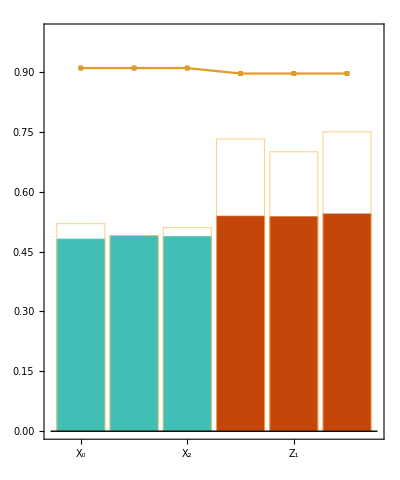
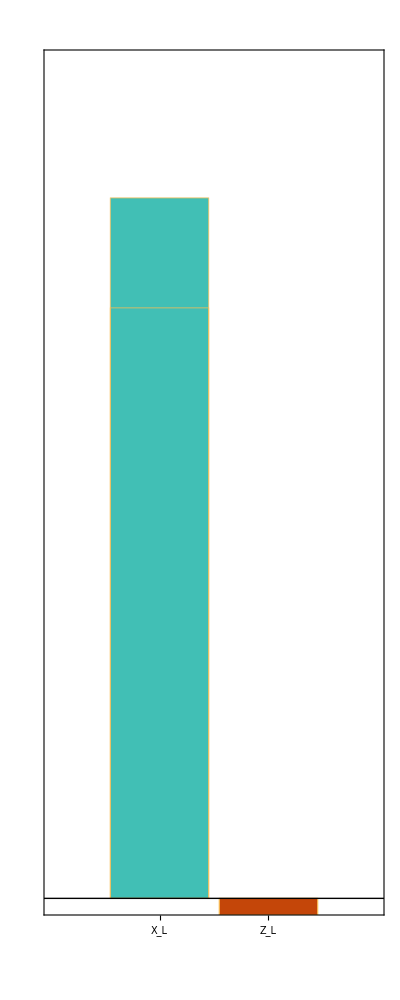

(2) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

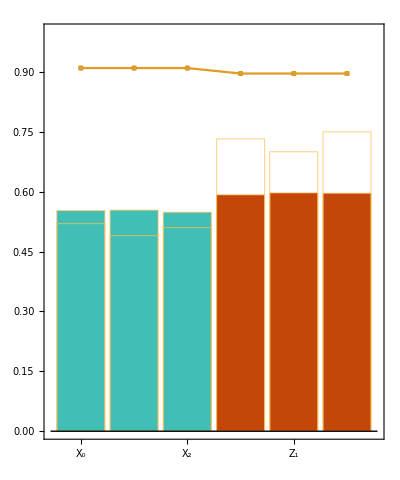
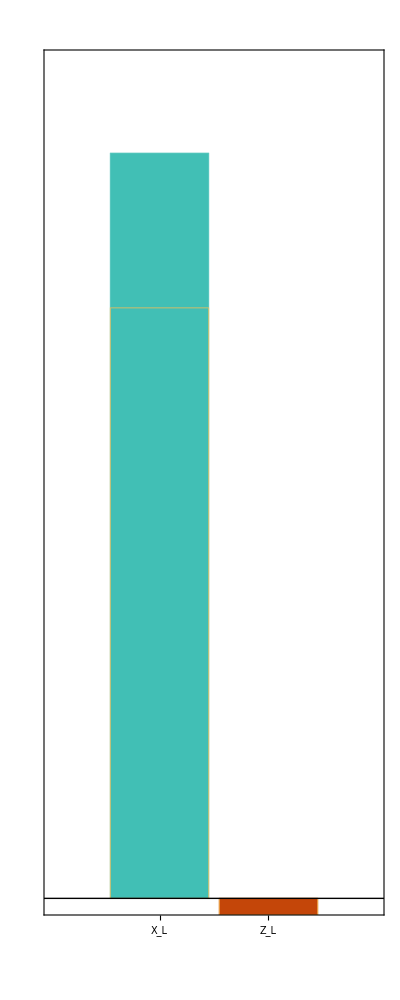

(3) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

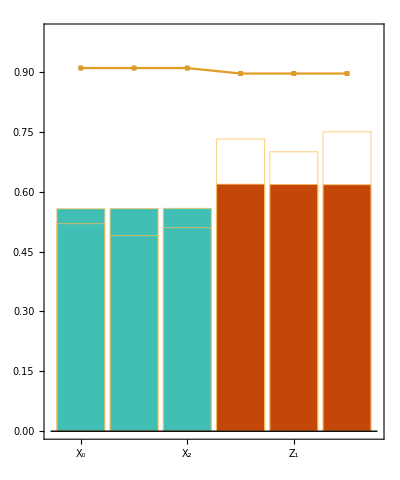
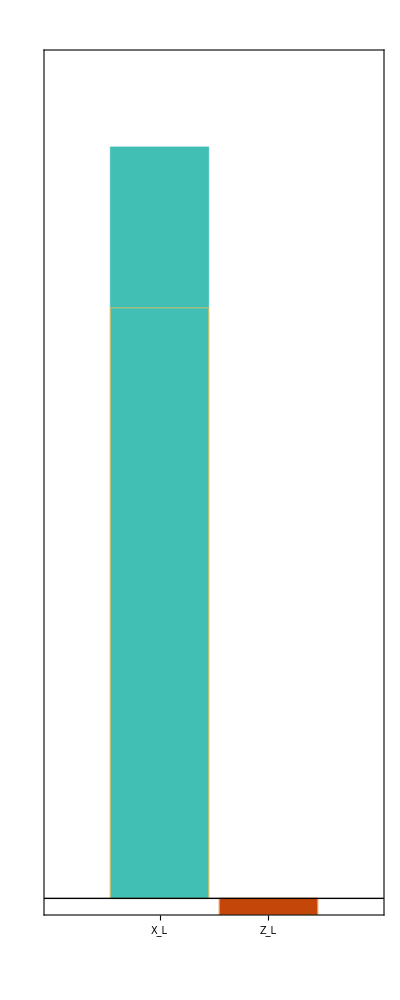

(4) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

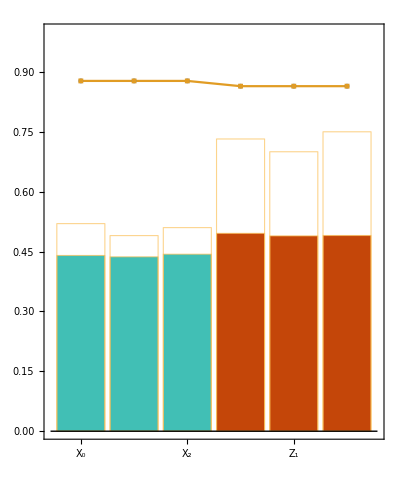
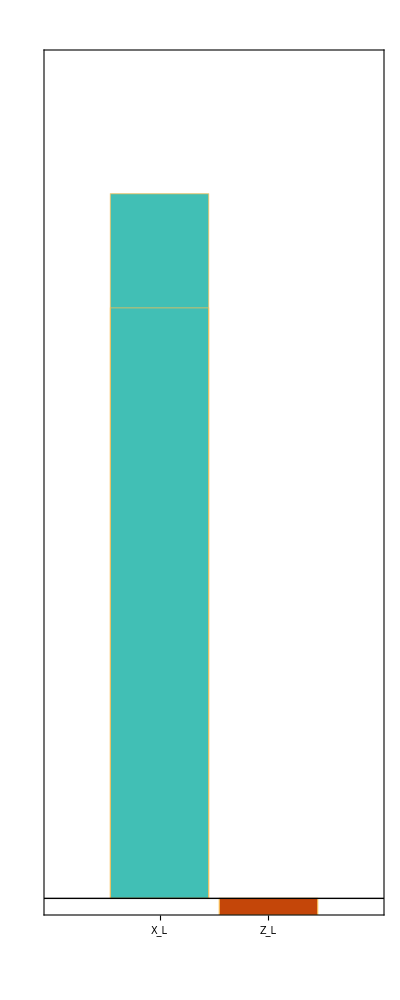

(5) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

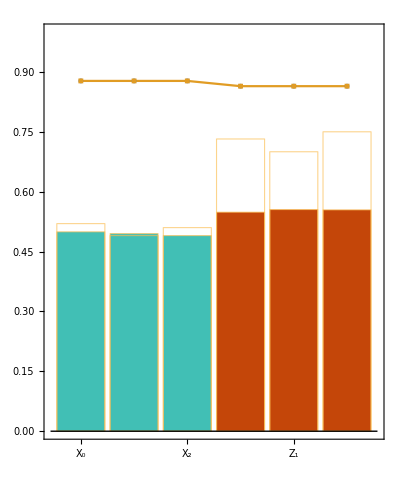
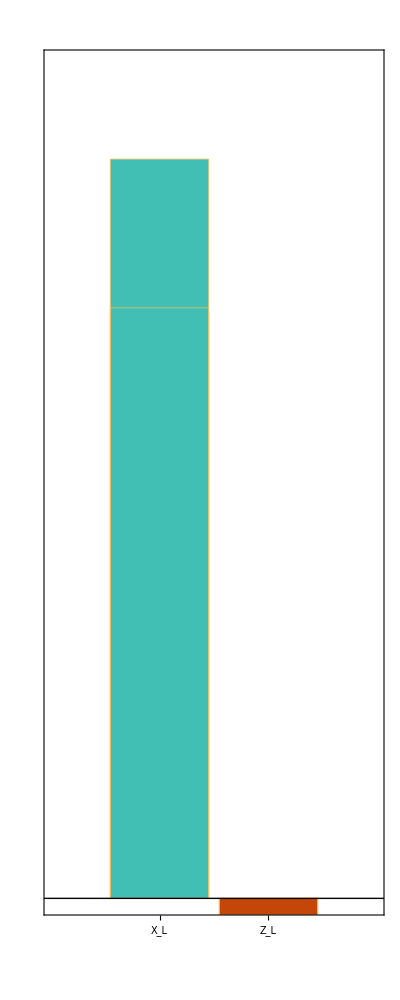

(6) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

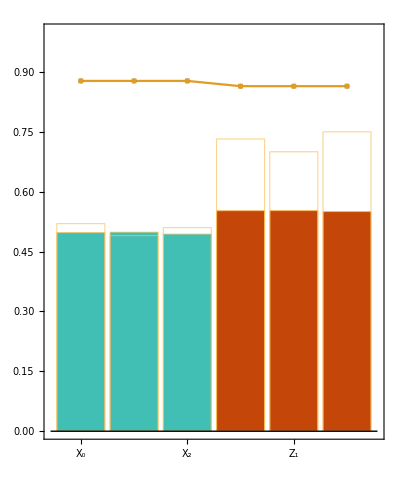
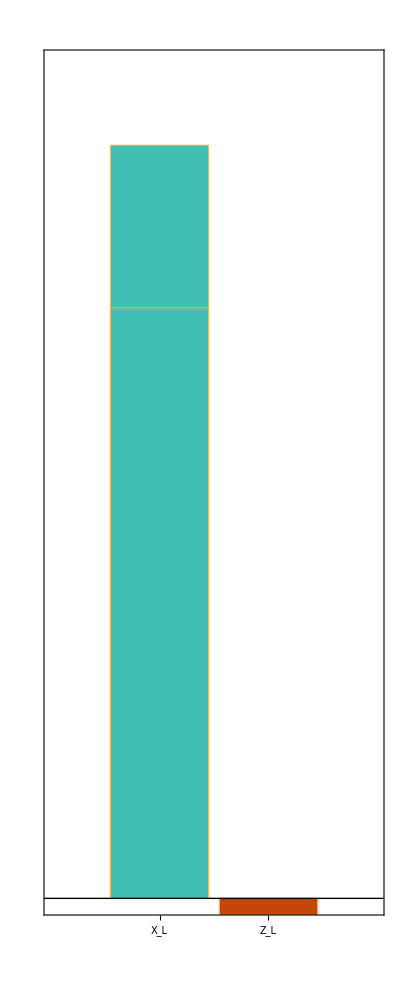

(7) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

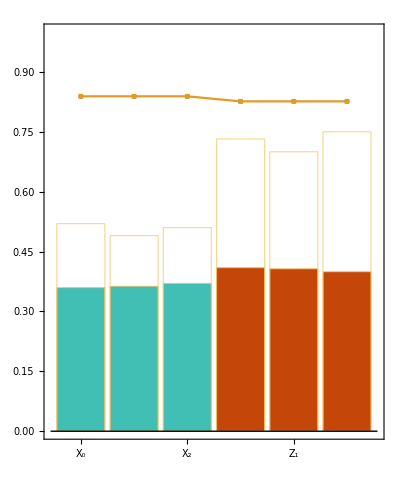
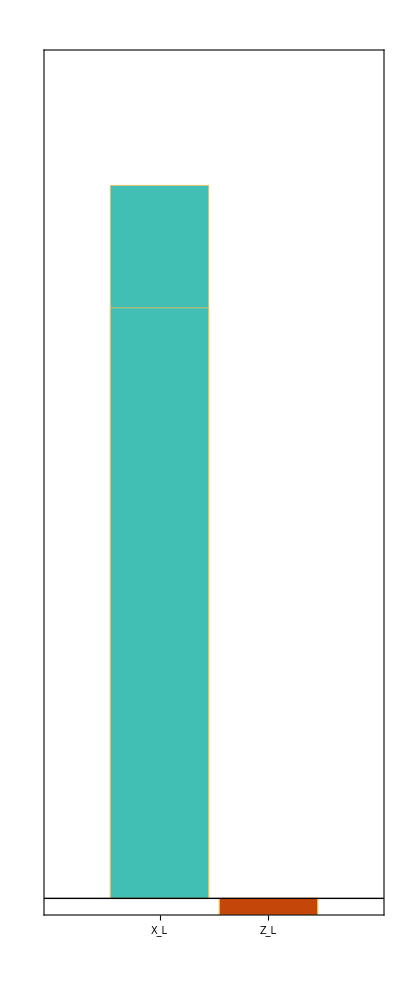

(8) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

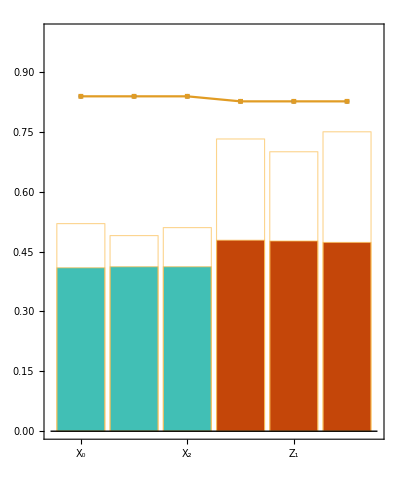
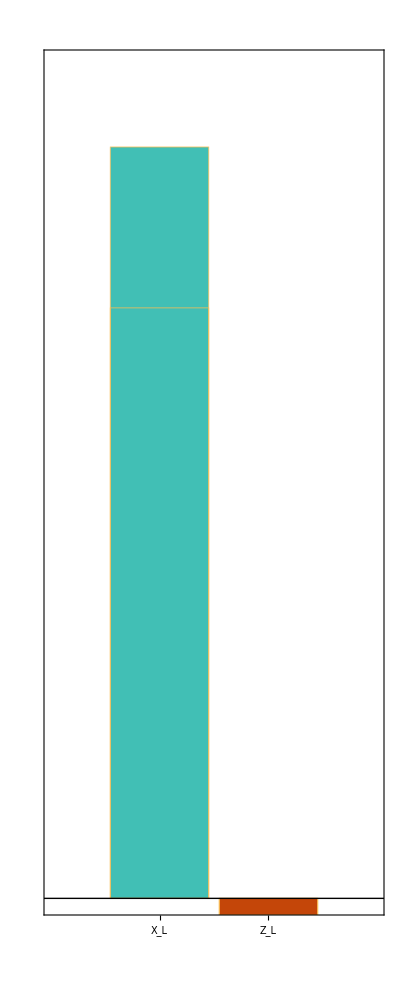

(9) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

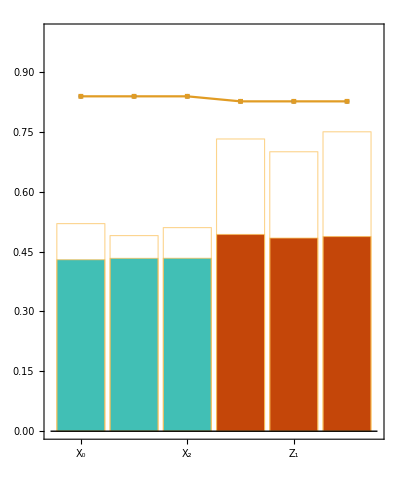
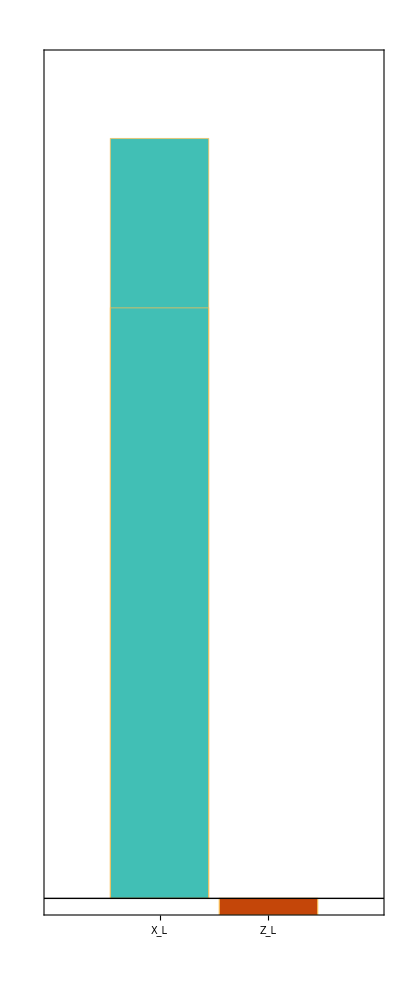

(10) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

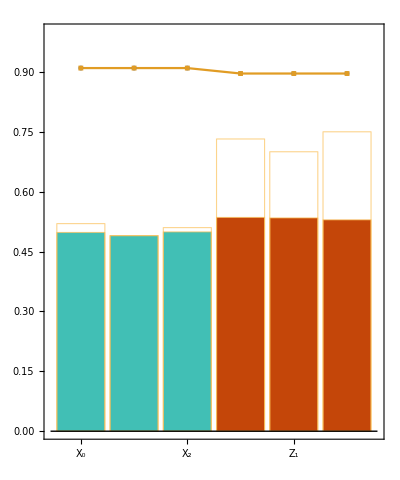
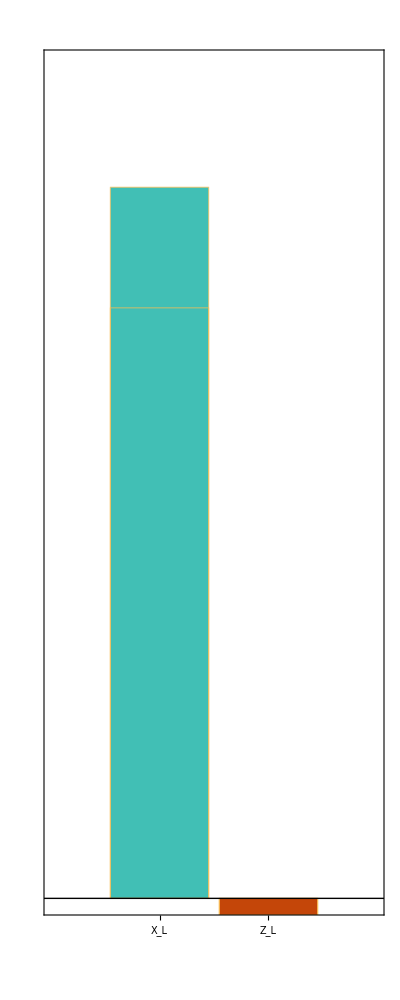

(11) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

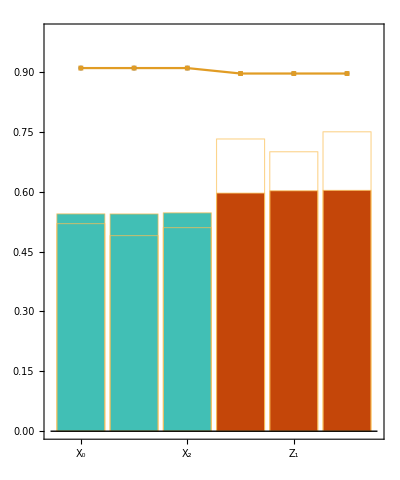
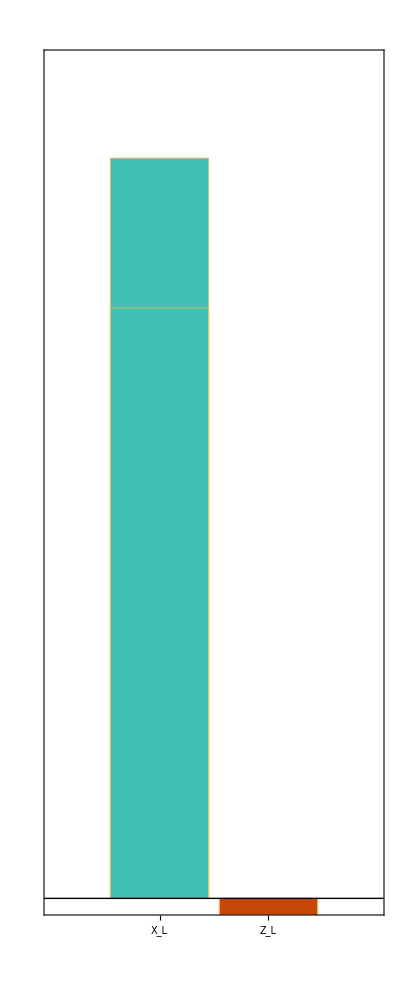

(12) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

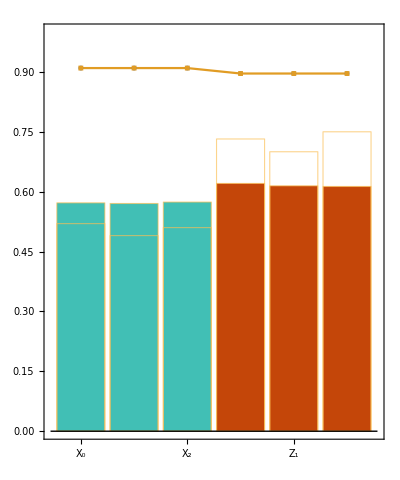
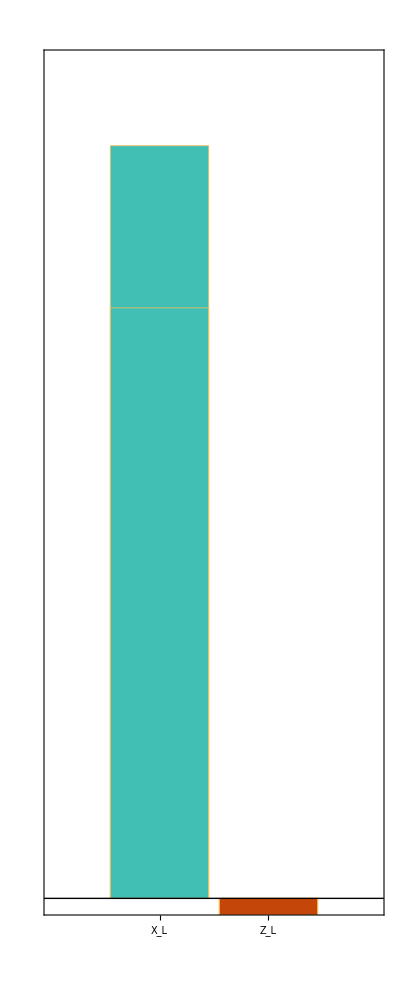

(13) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

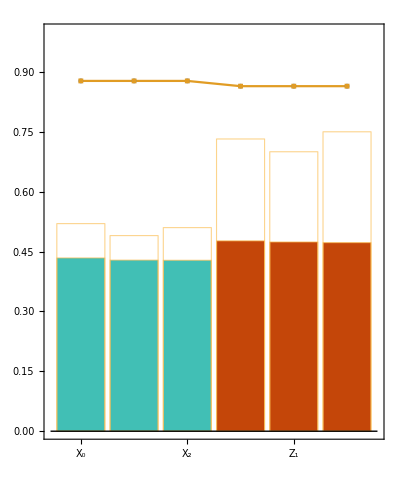
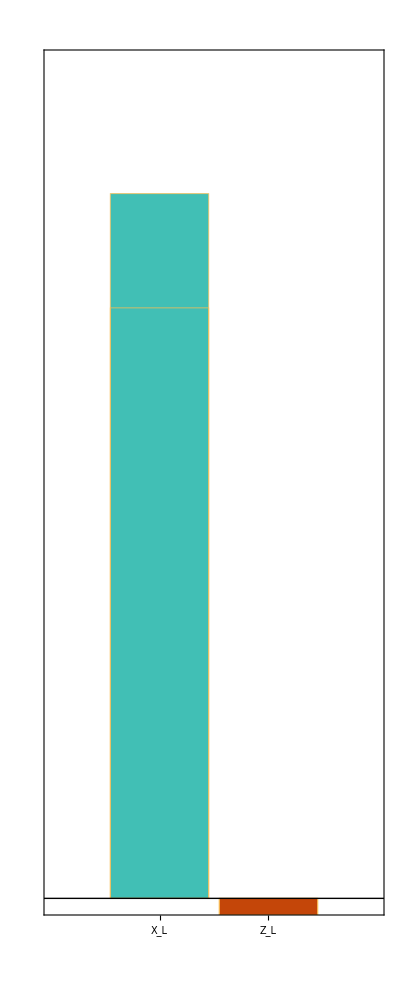

(14) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

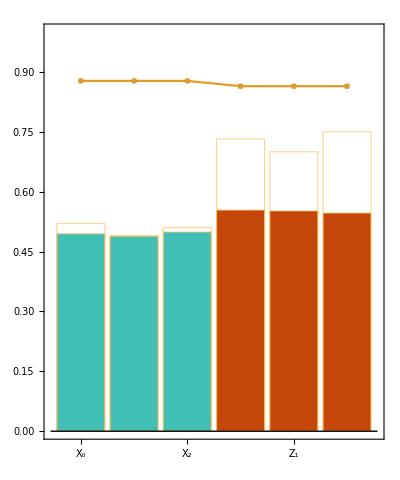
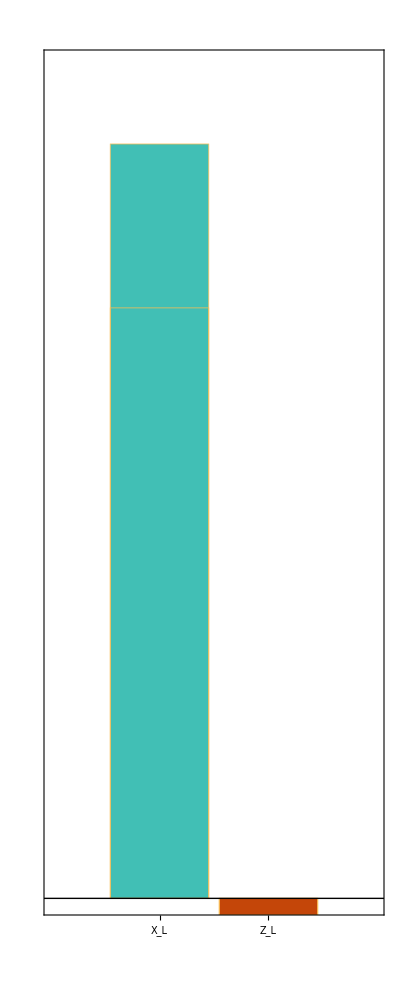

(15) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

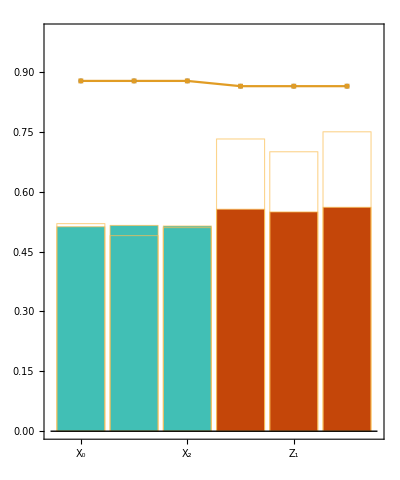
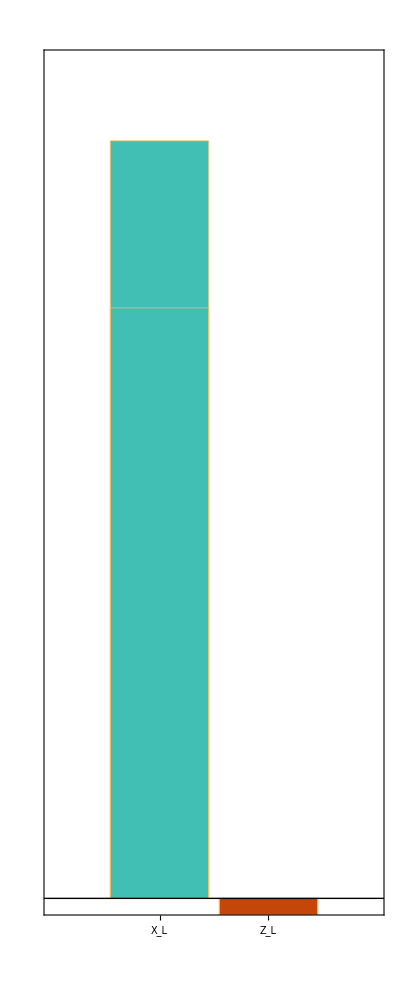

(16) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

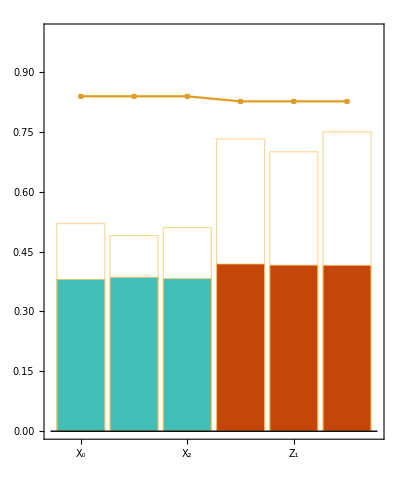
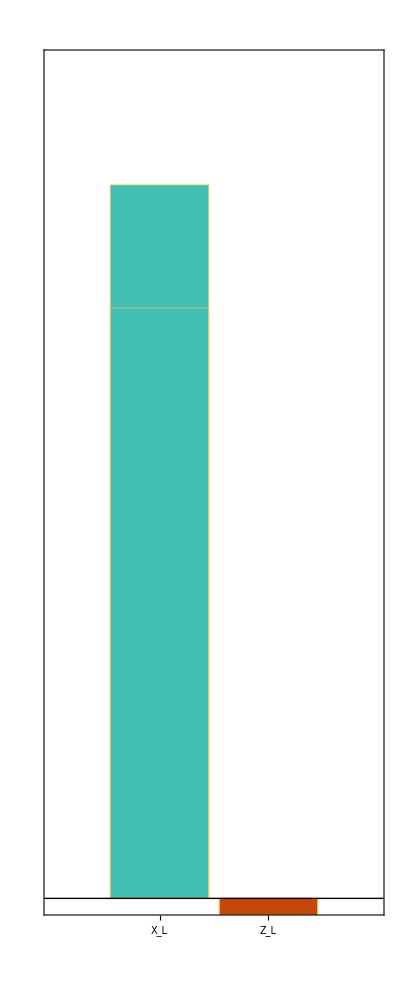

(17) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

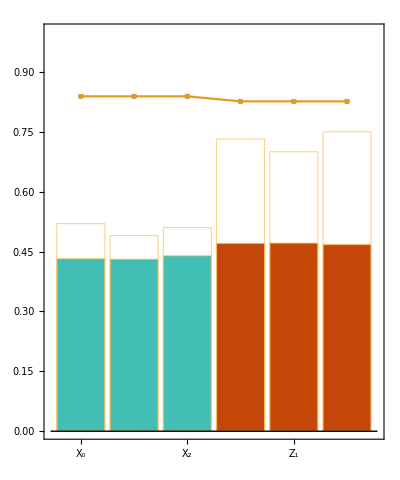
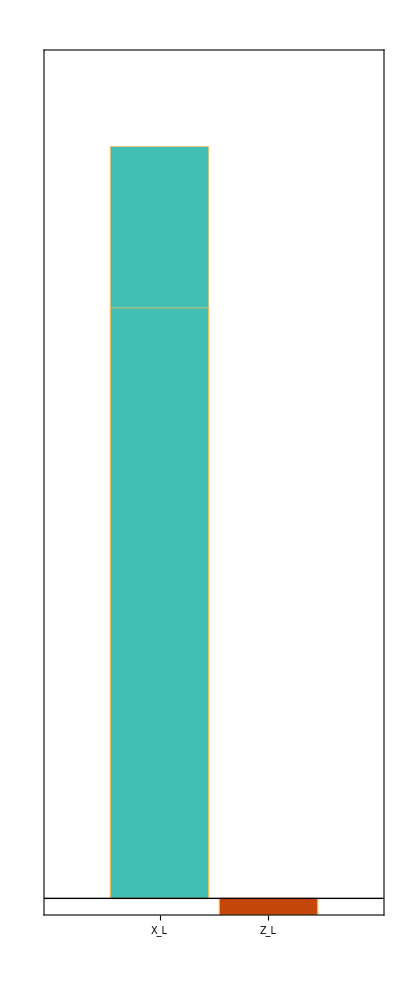

(18) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

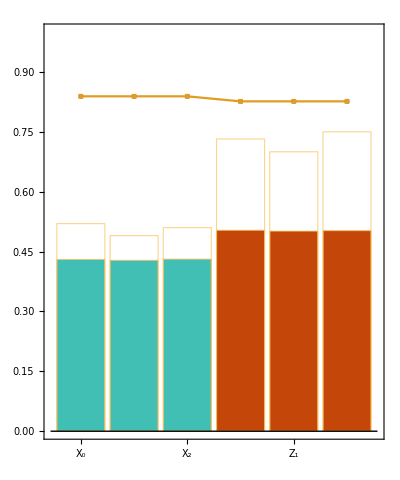
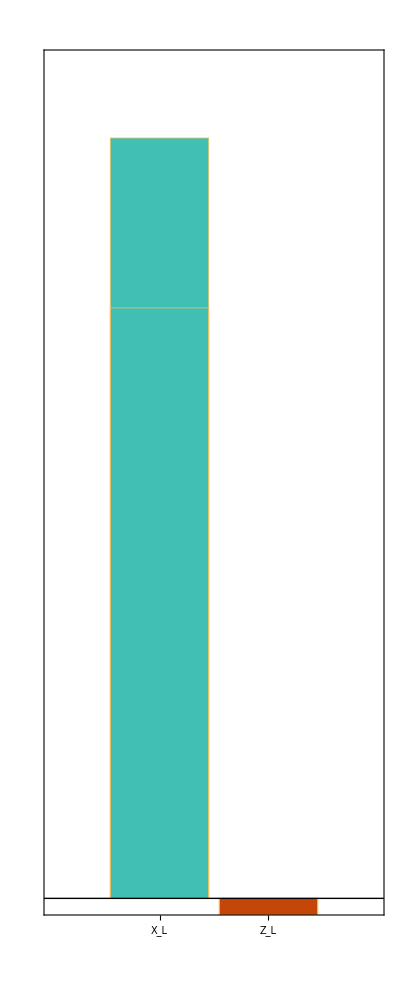

(19) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

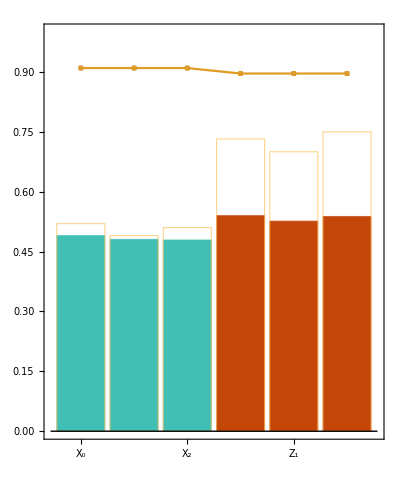
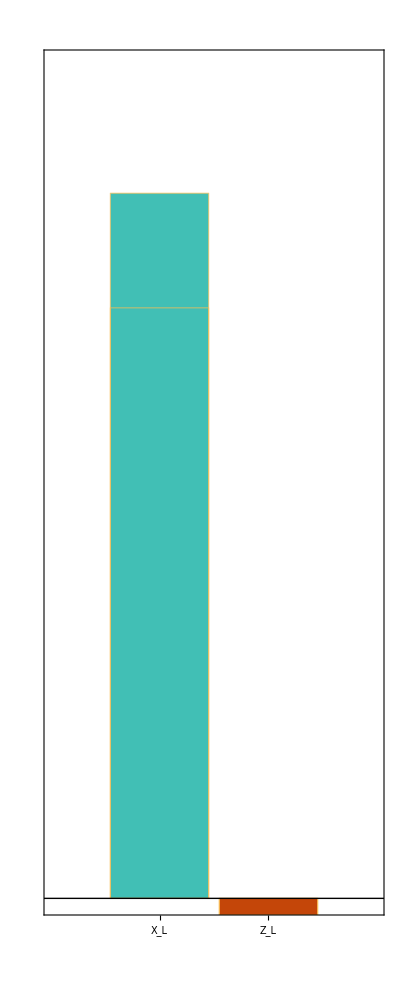

(20) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

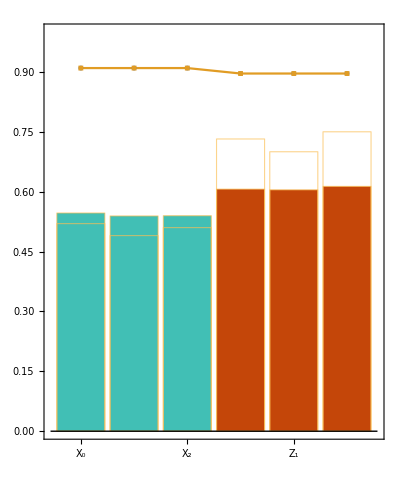
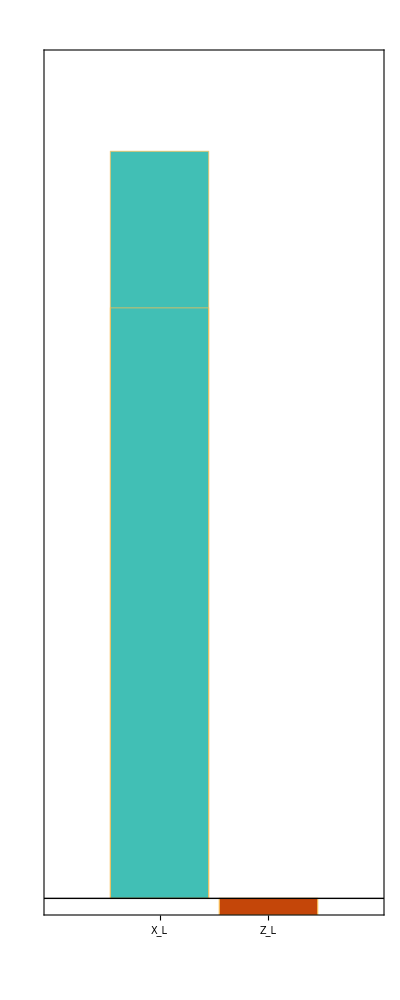

(21) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

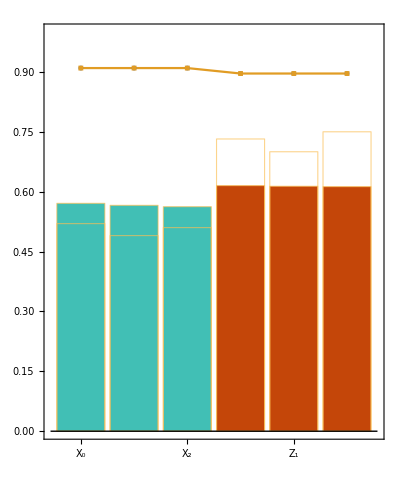
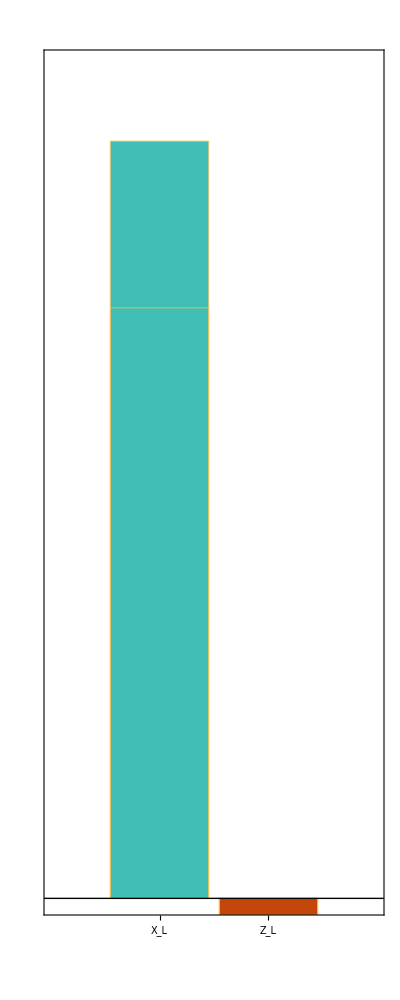

(22) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

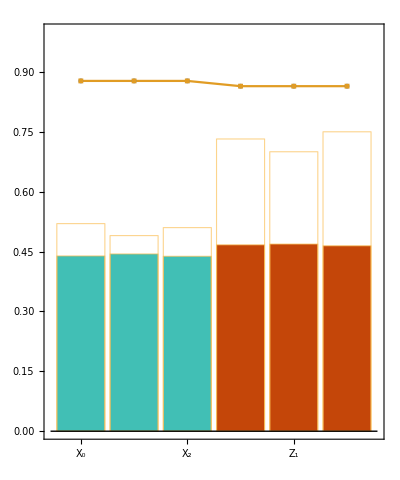
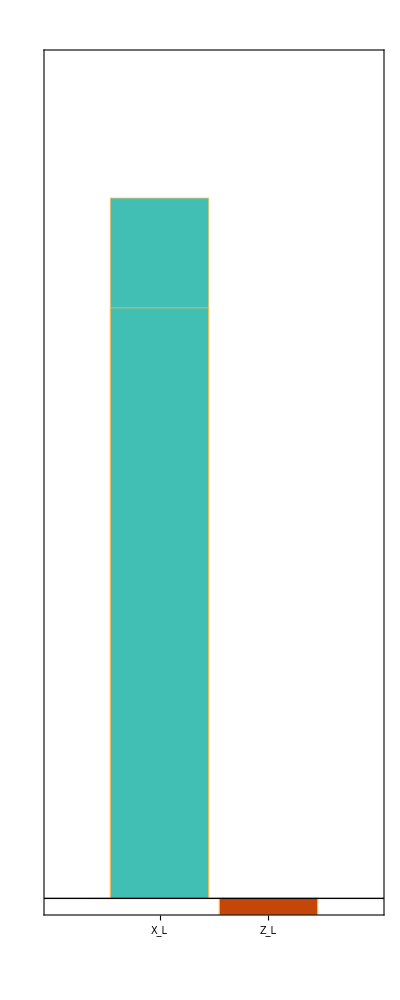

(23) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

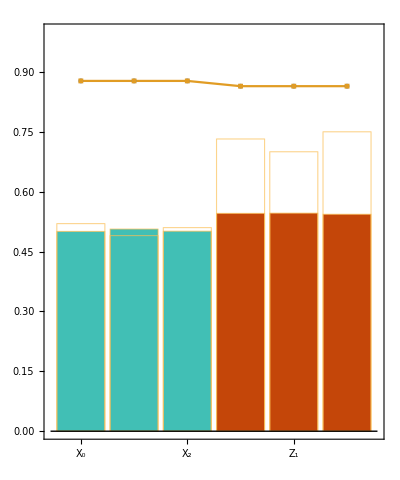
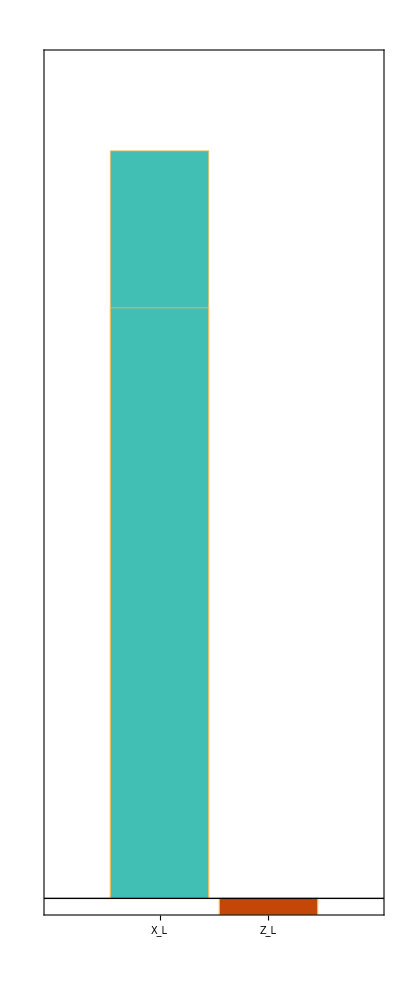

(24) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

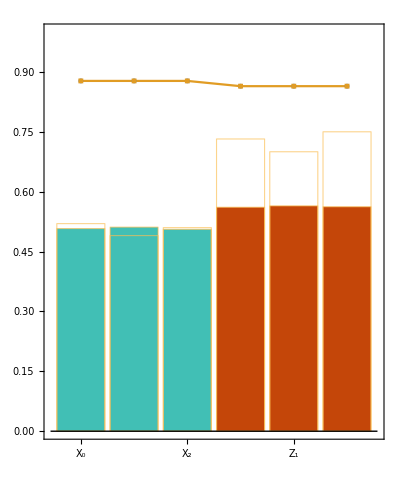
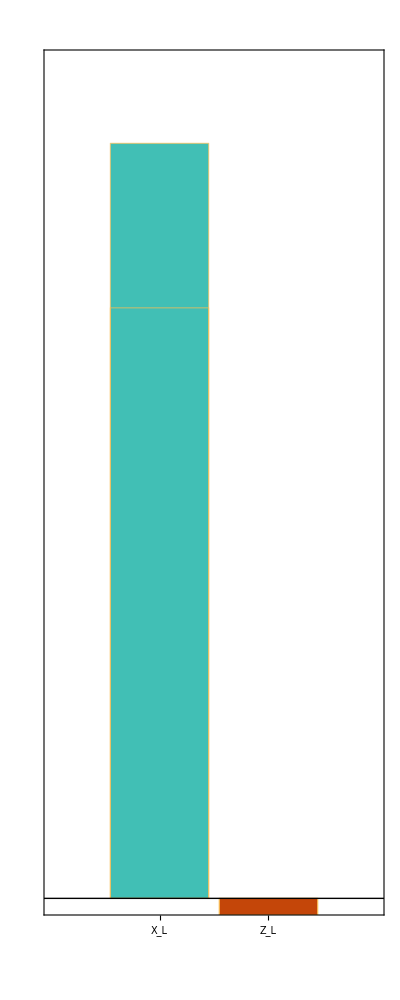

(25) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

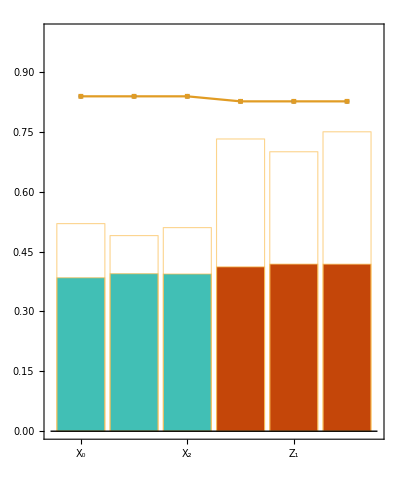
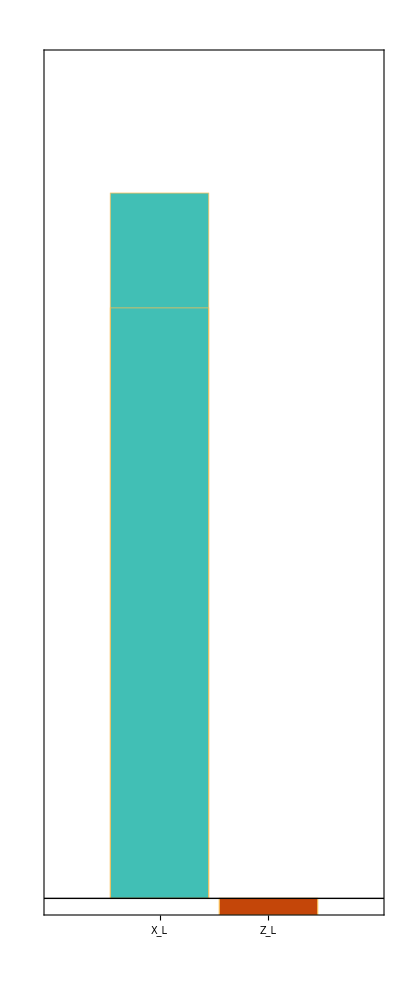

(26) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

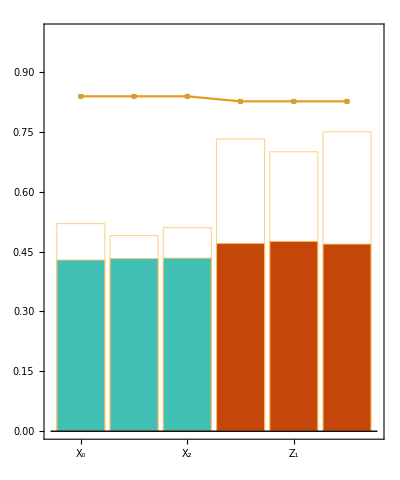
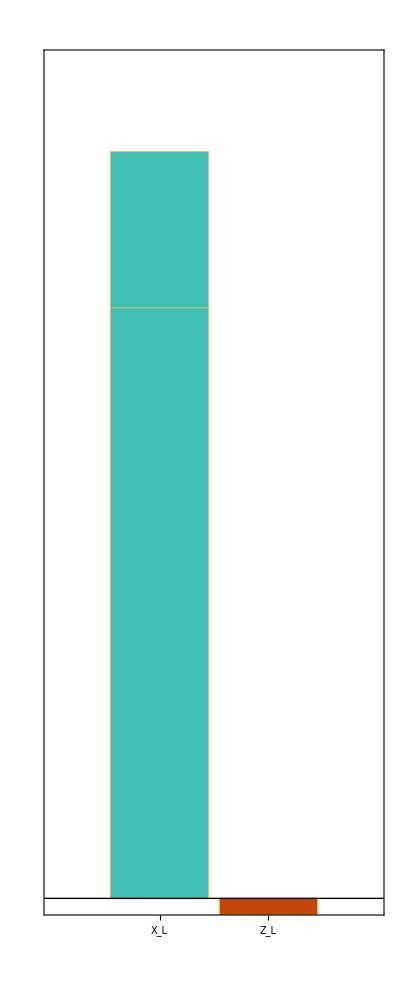

(27) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

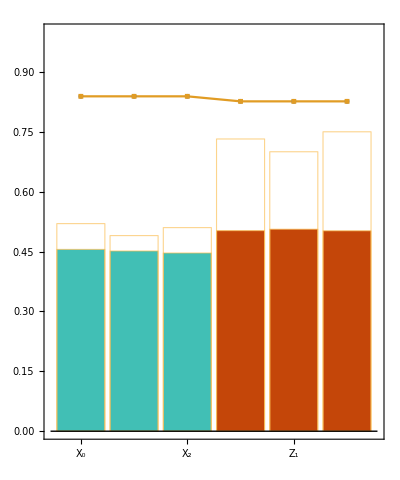
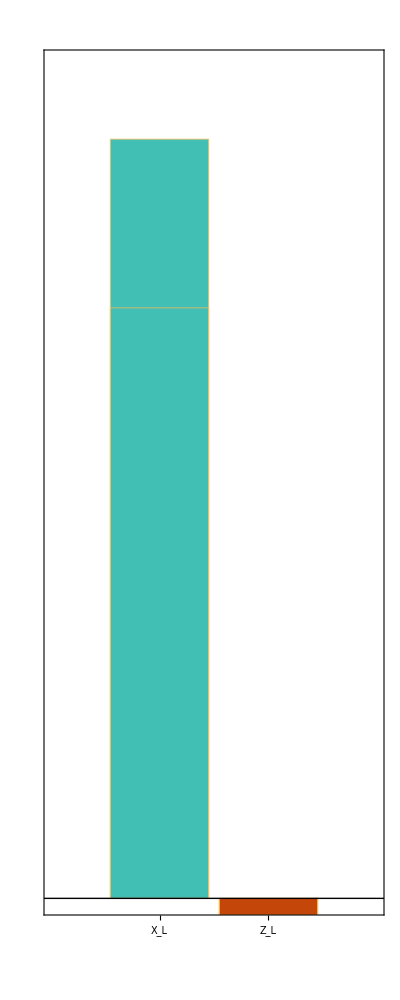

(28) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

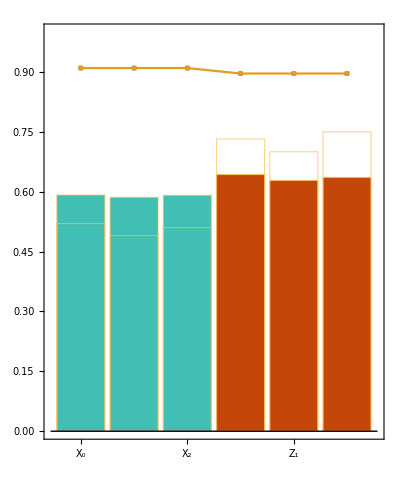
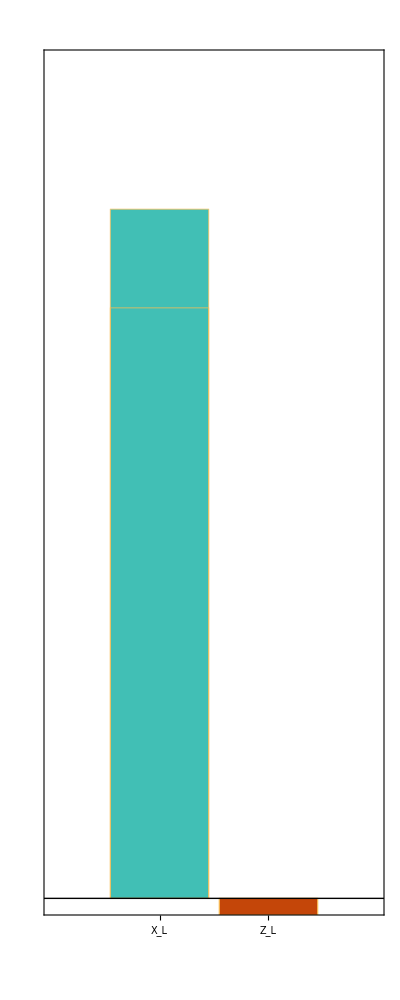

(29) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

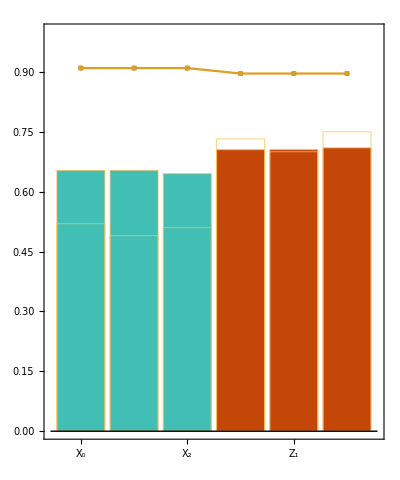
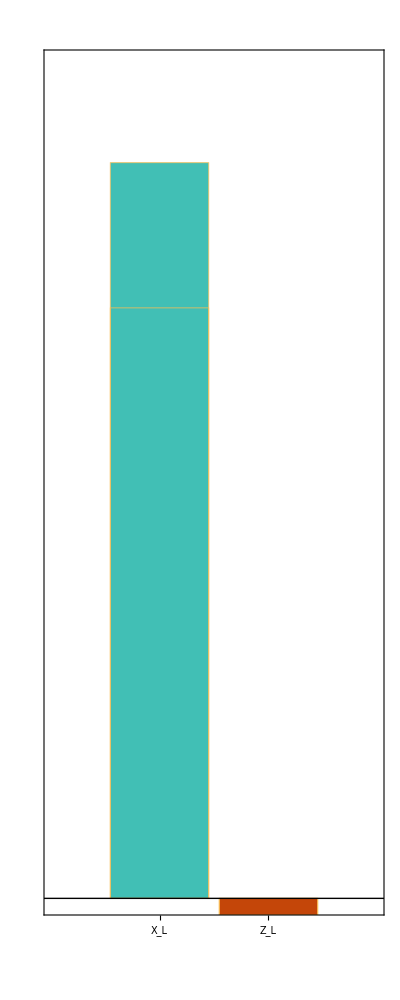

(30) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

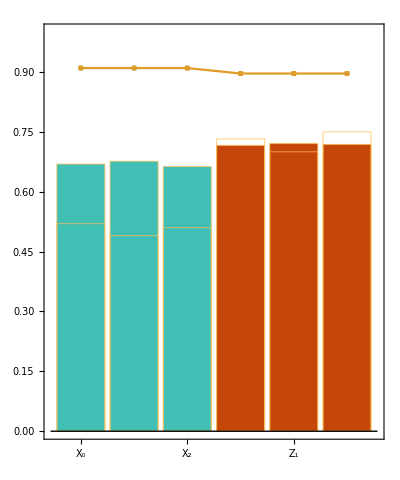
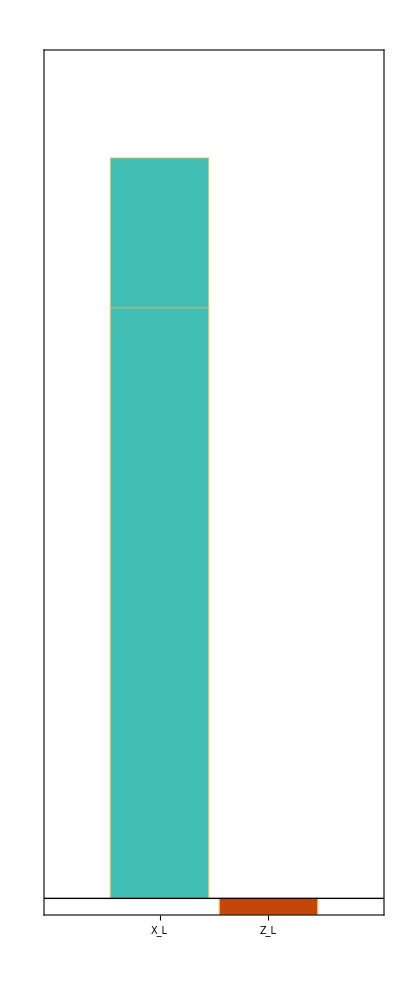

(31) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

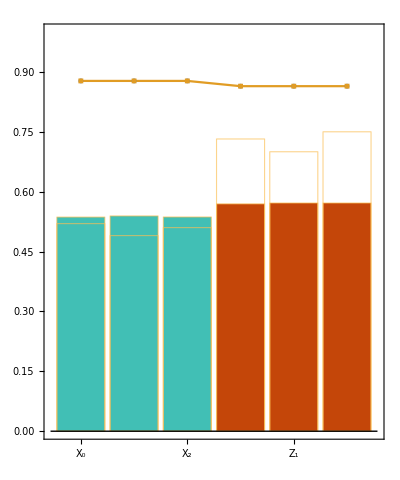
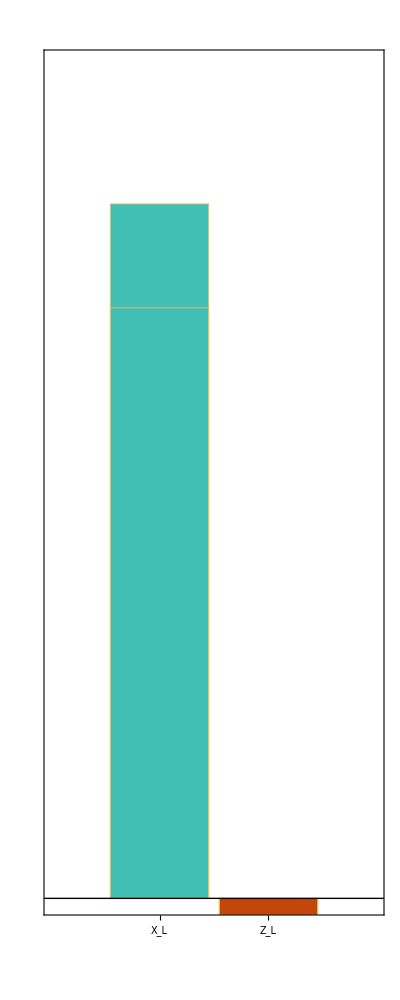

(32) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

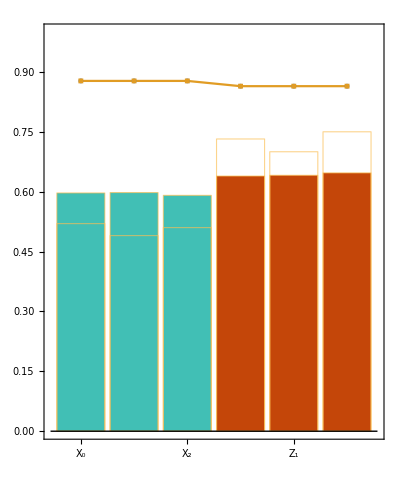
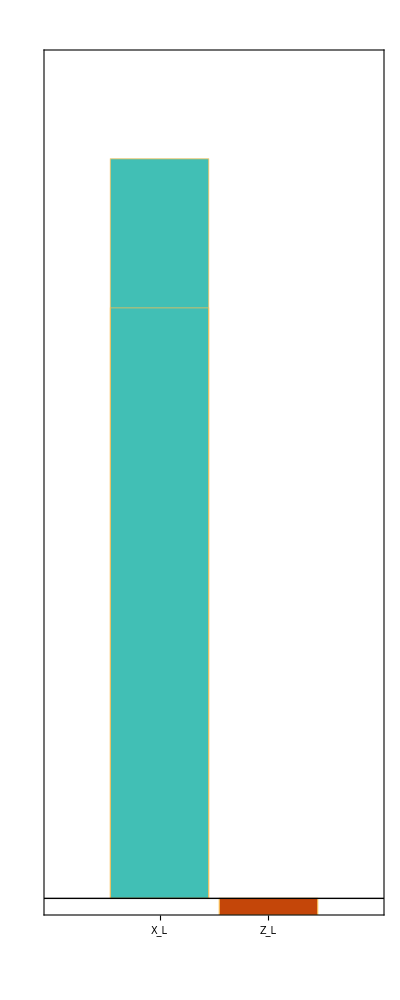

(33) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

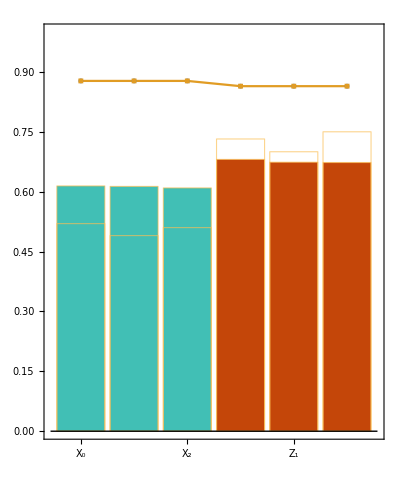
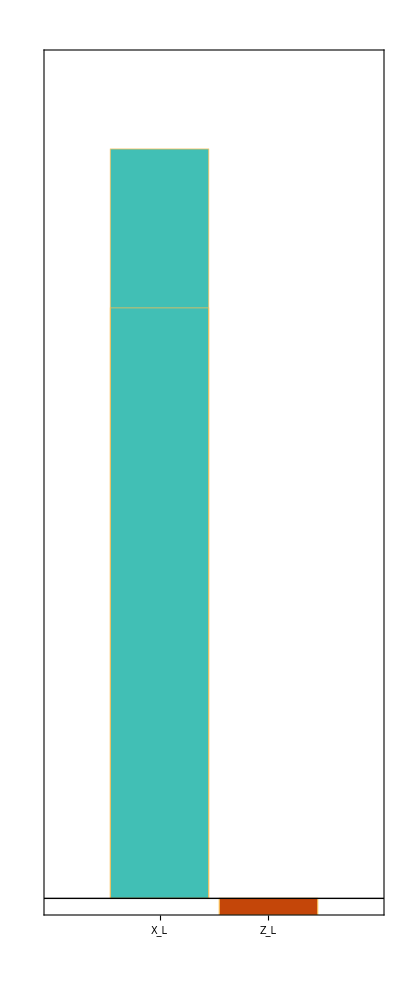

(34) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

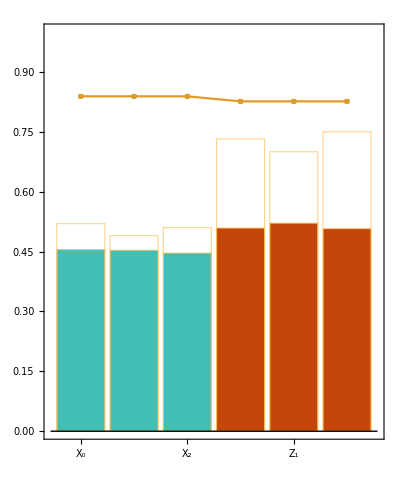
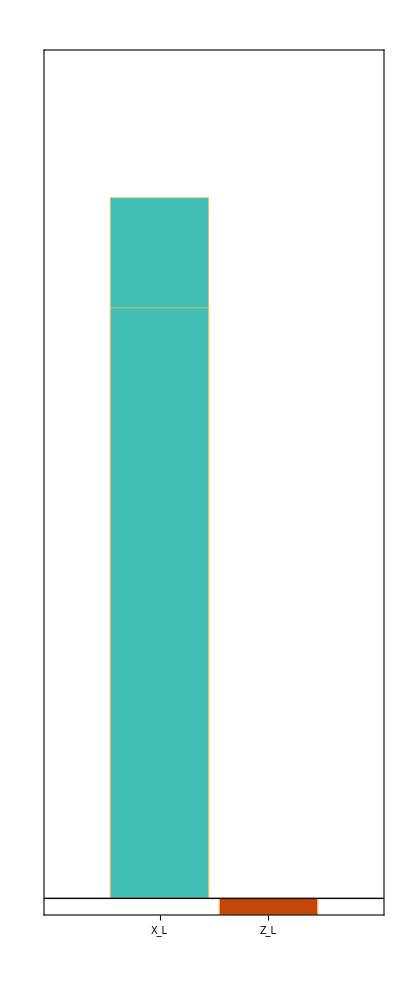

(35) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

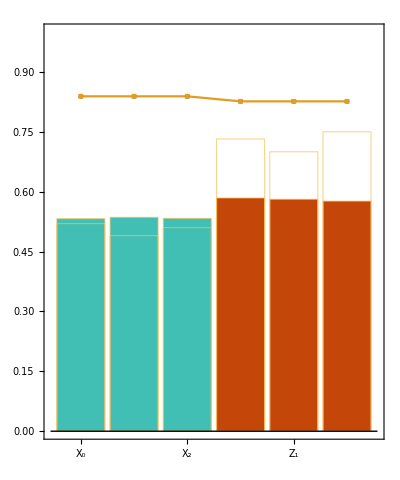
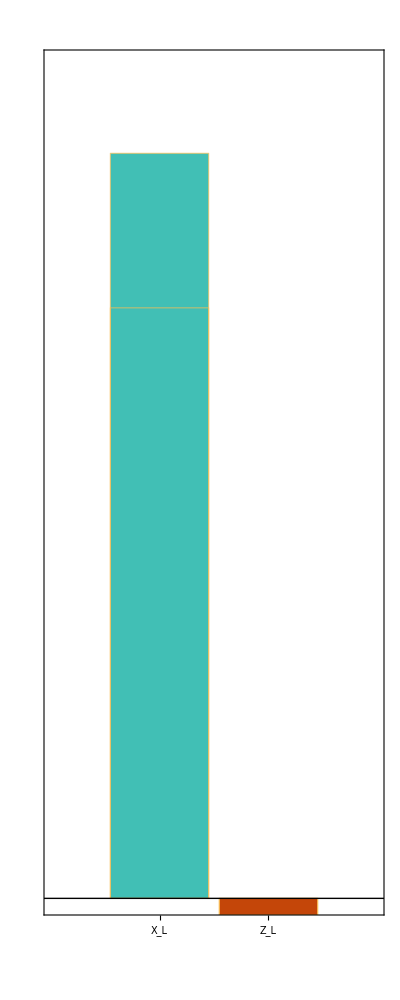

(36) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

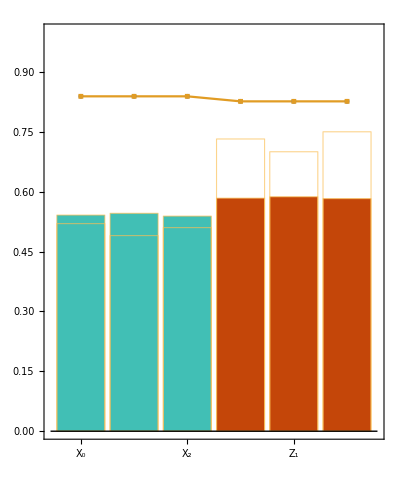
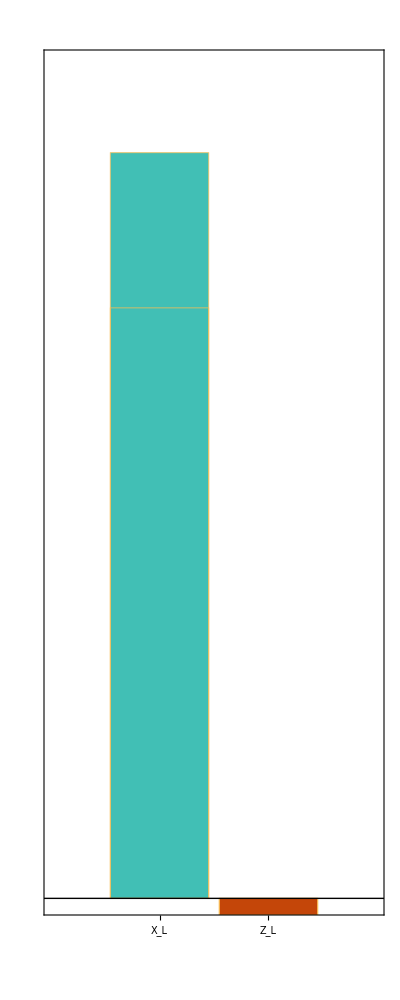

(37) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

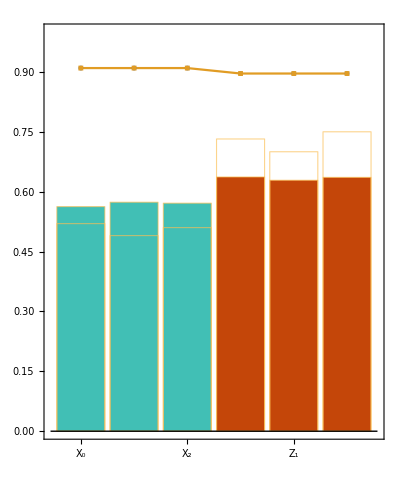
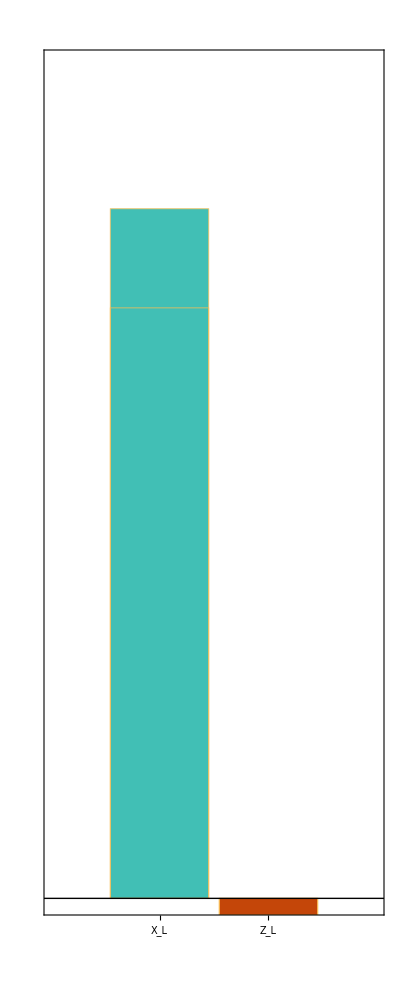

(38) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

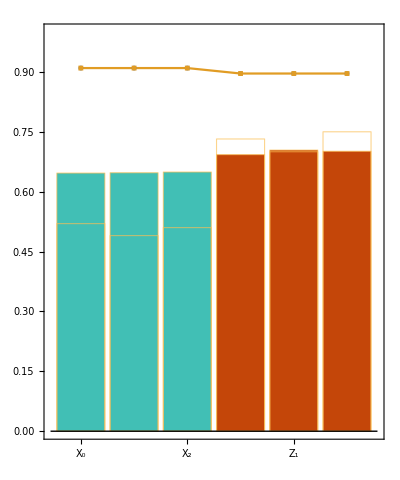
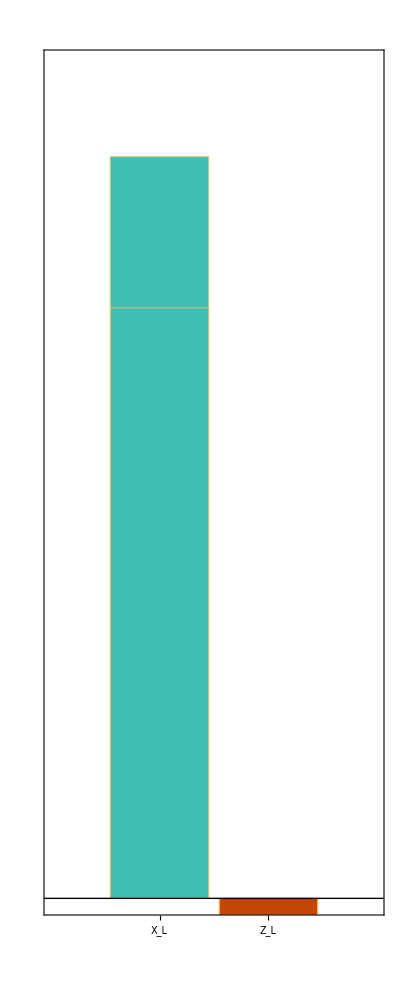

(39) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

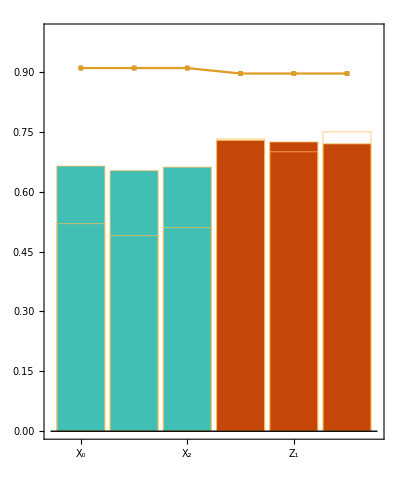
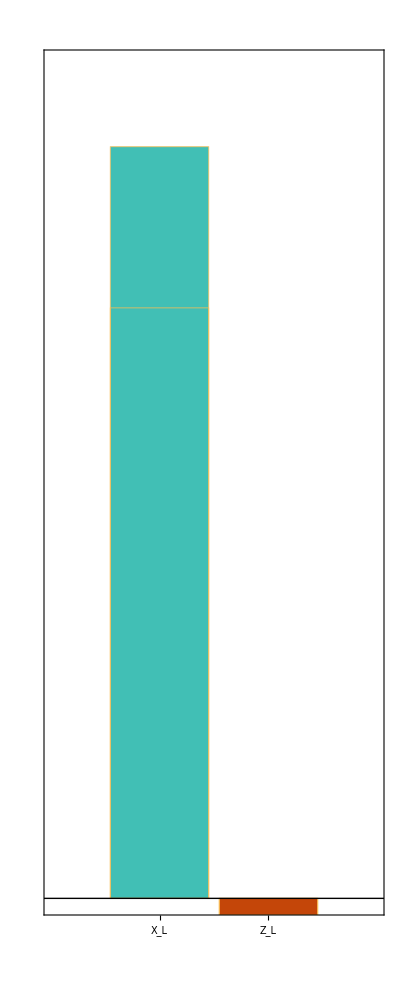

(40) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

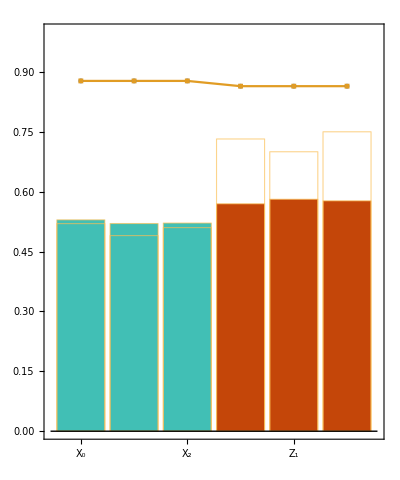
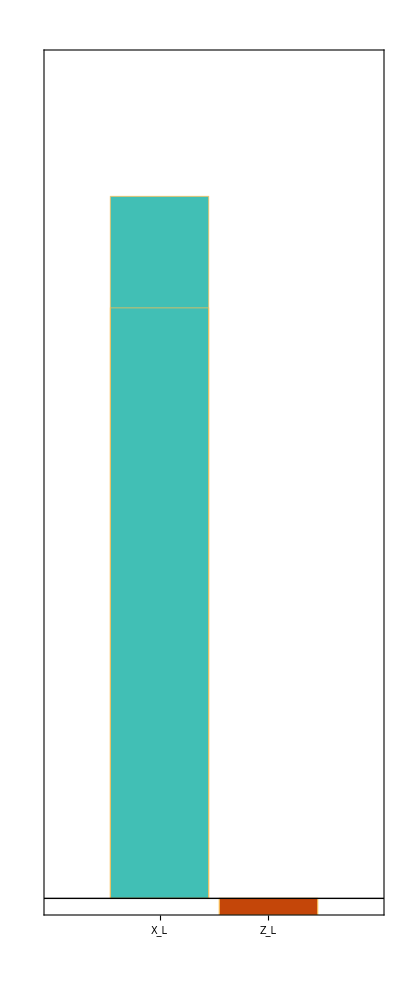

(41) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

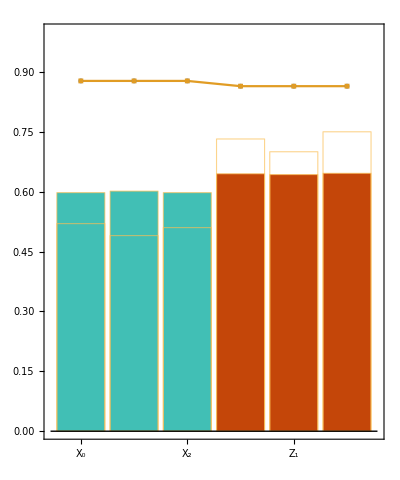
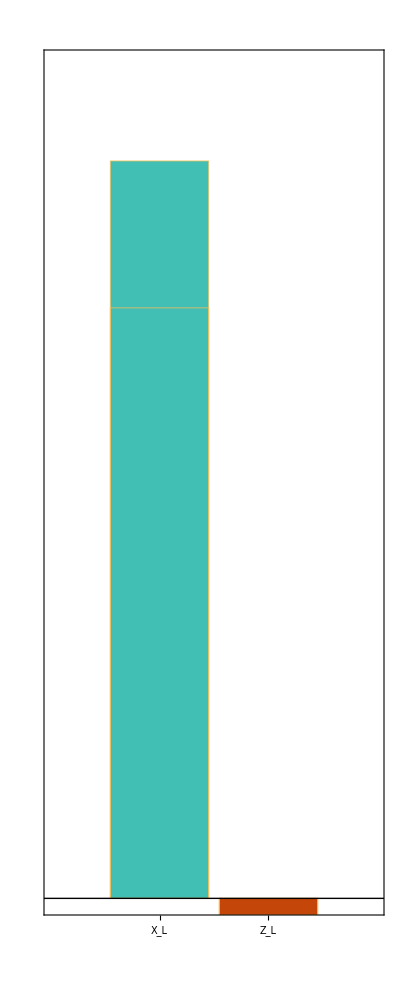

(42) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

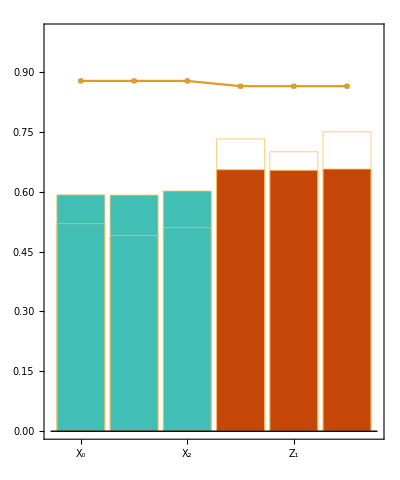
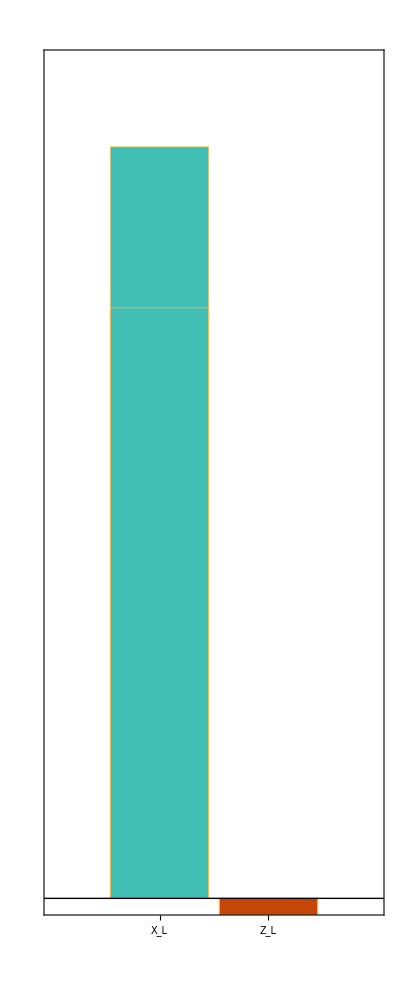

(43) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

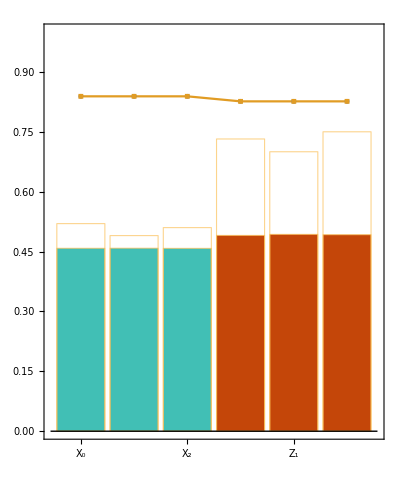
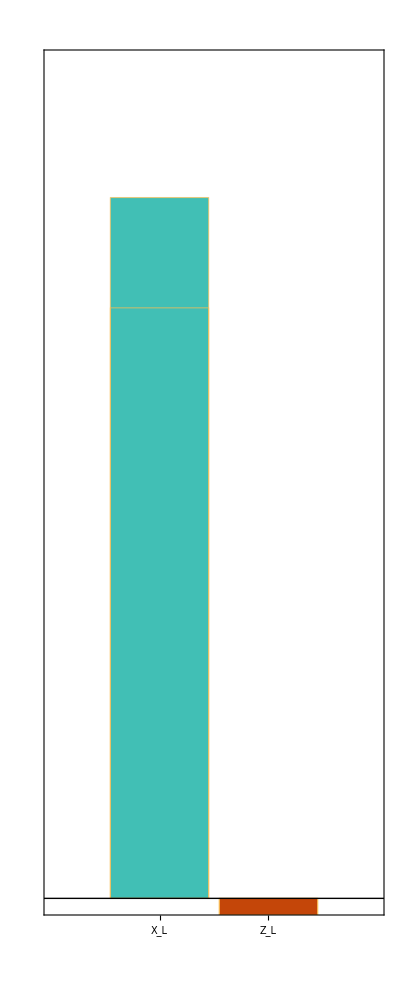

(44) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

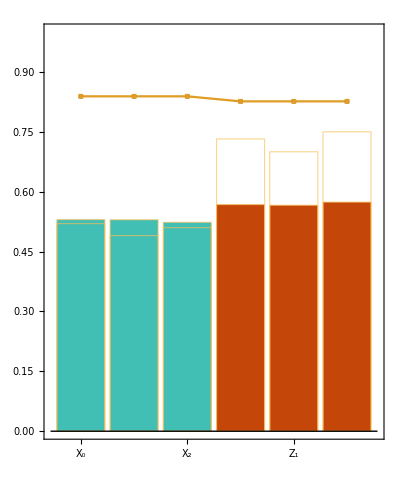
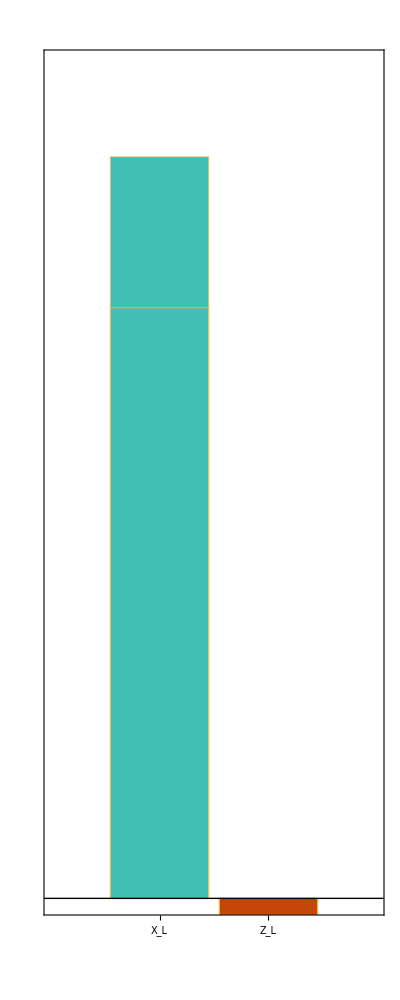

(45) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

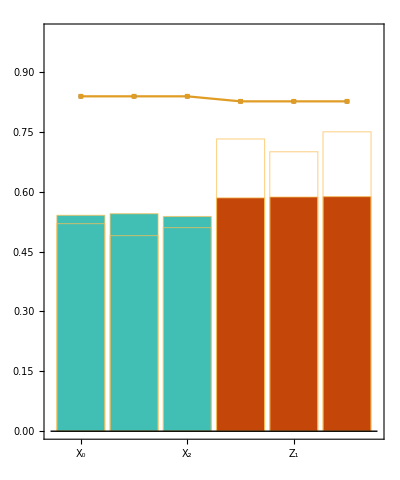
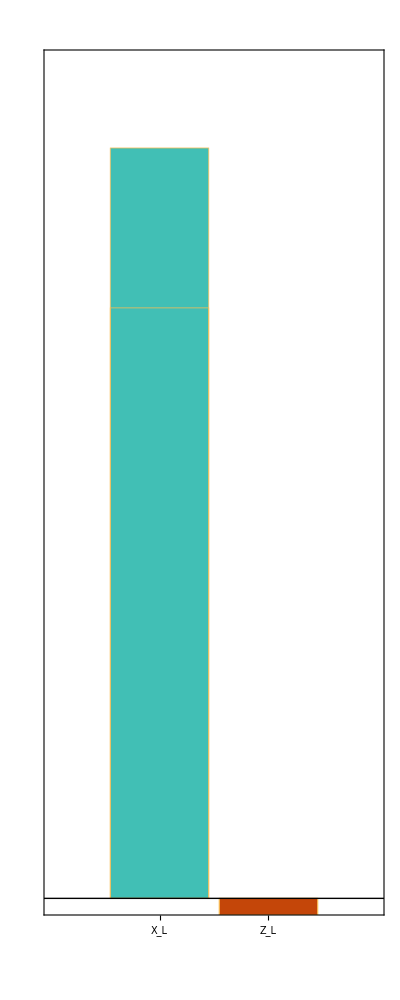

(46) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

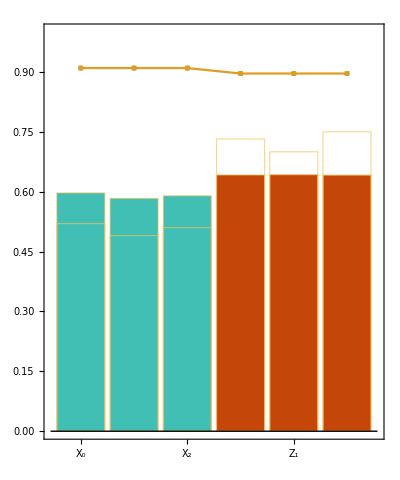
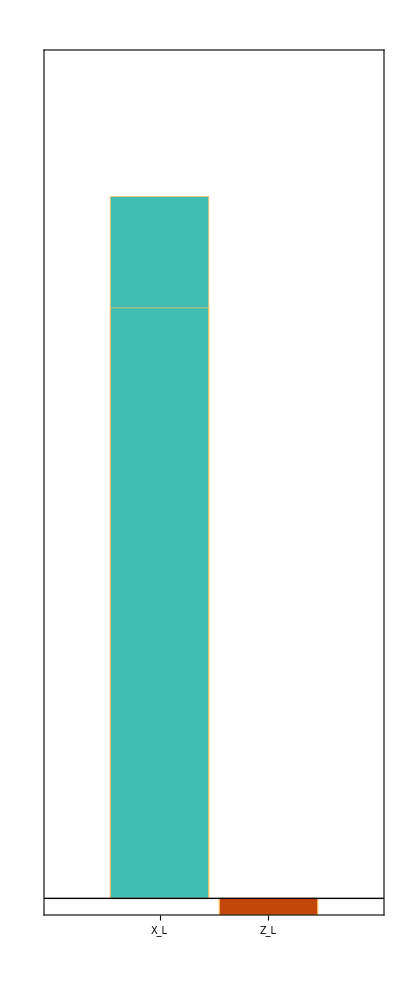

(47) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

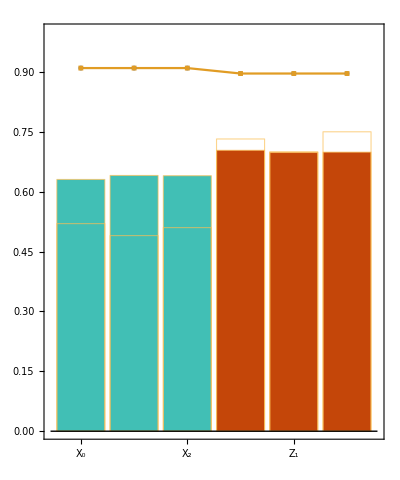
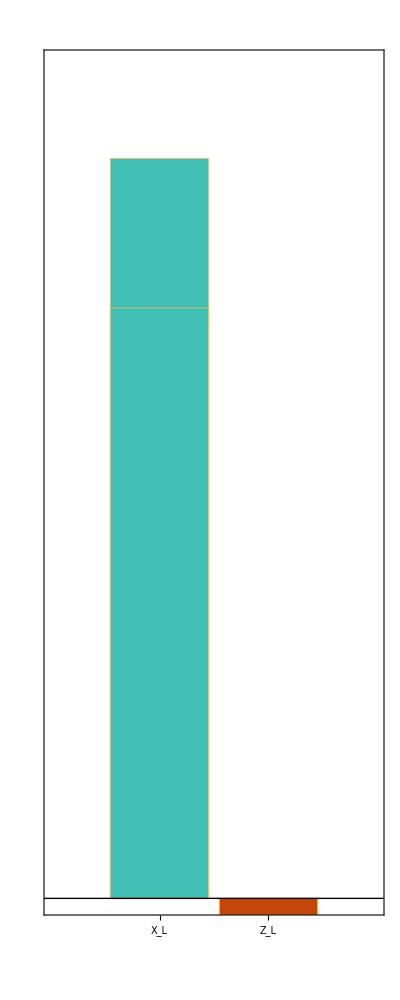

(48) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

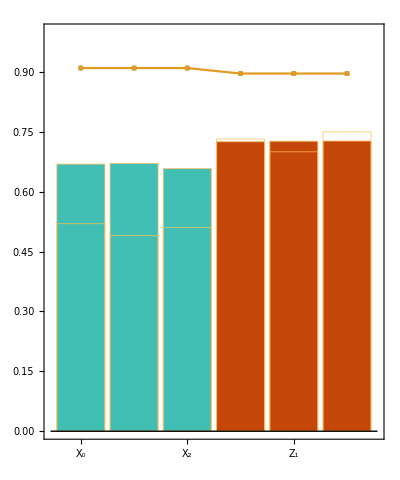
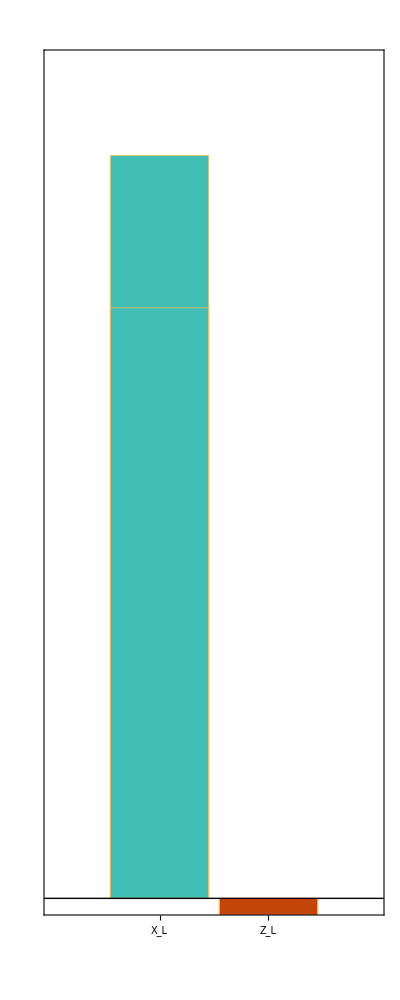

(49) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

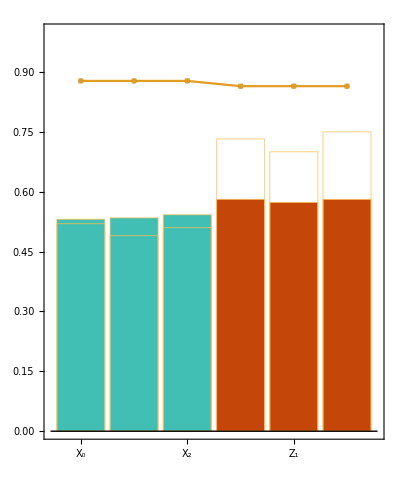
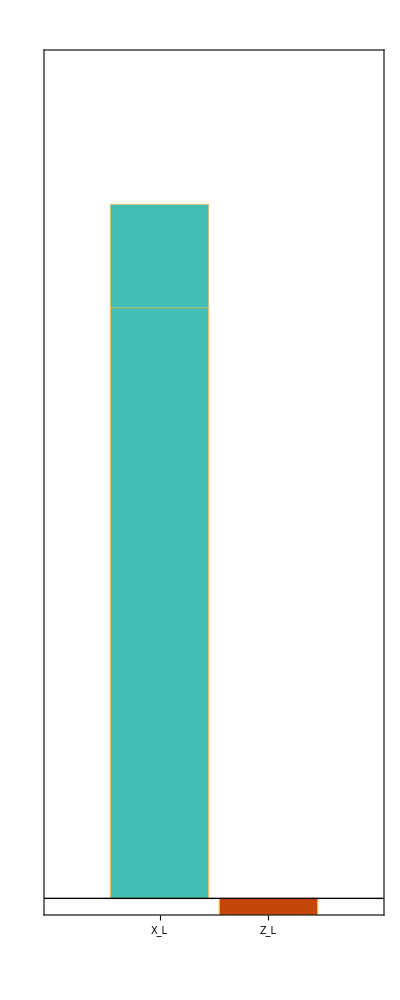

(50) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

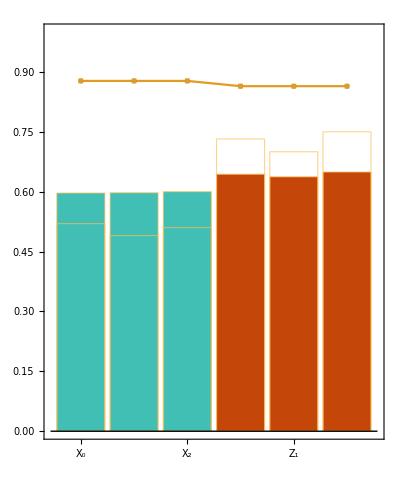
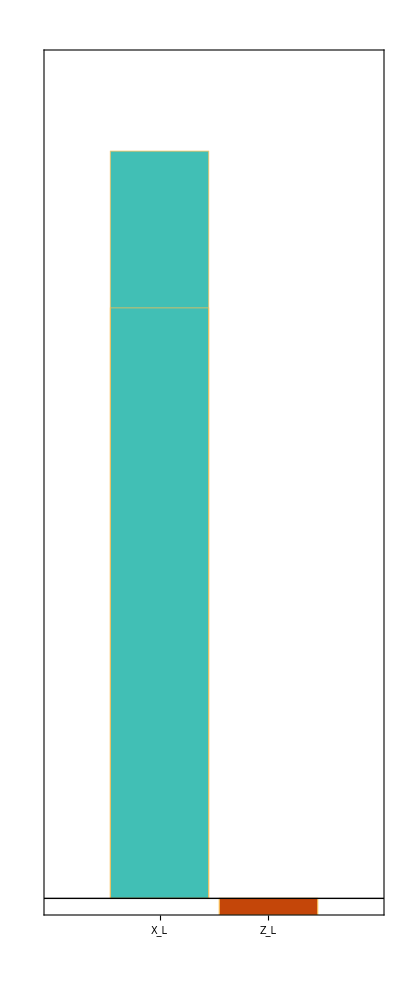

(51) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

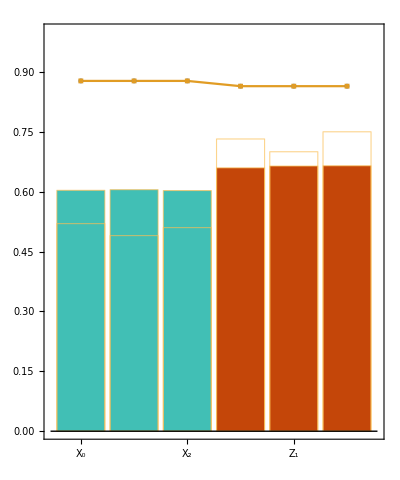
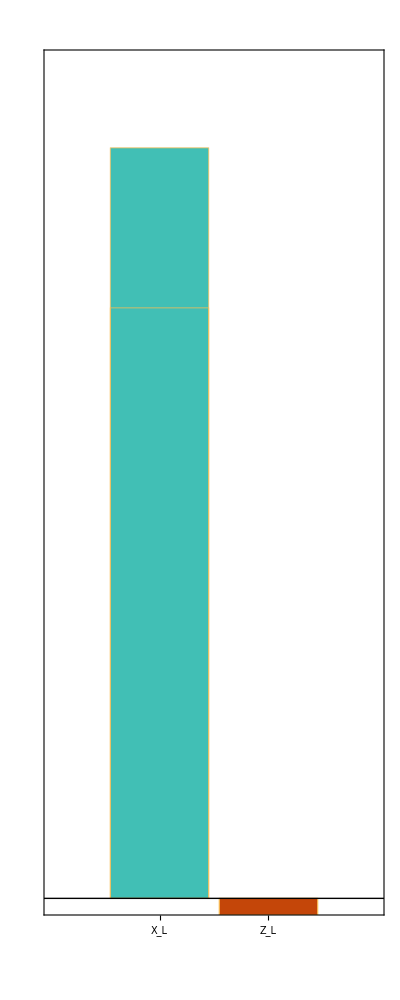

(52) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

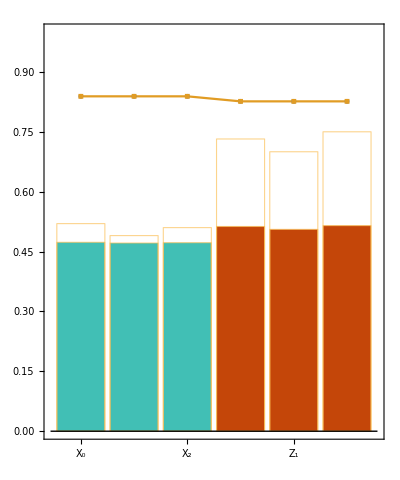
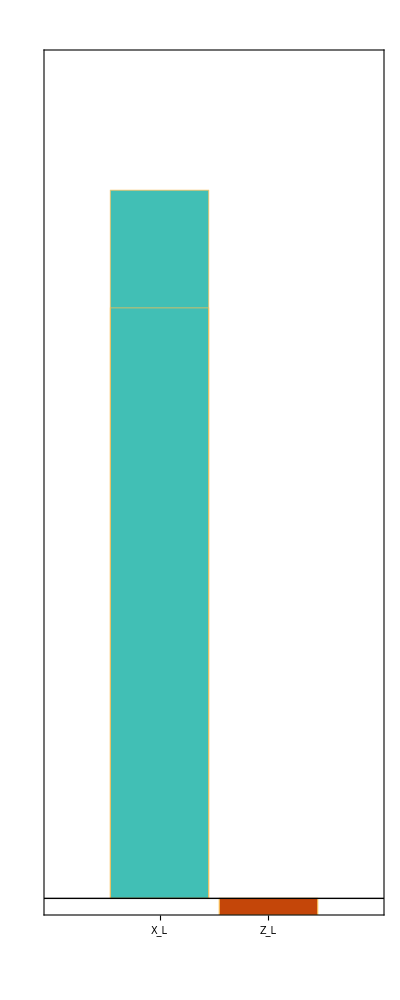

(53) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

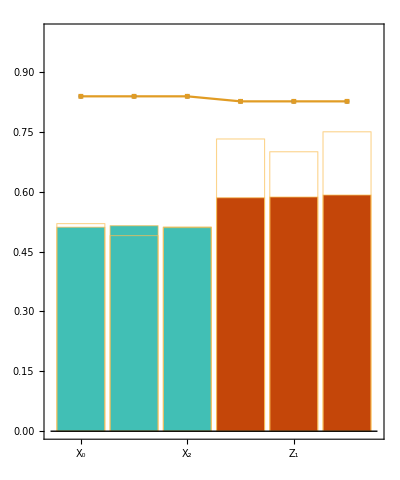
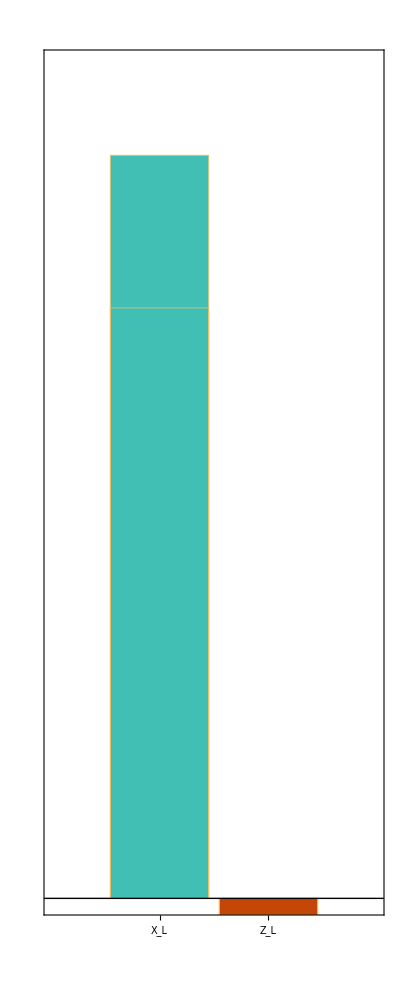

(54) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

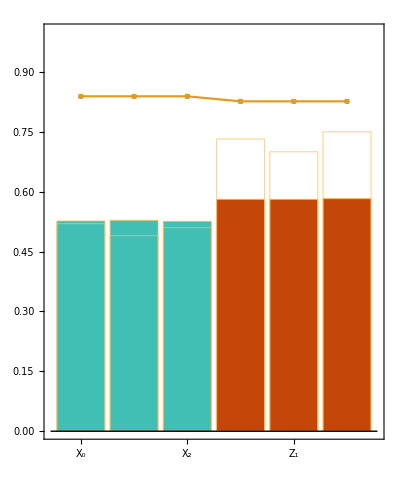
-Graphics--Graphics-

(55) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

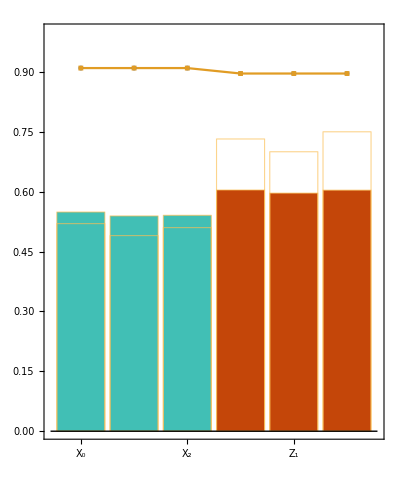
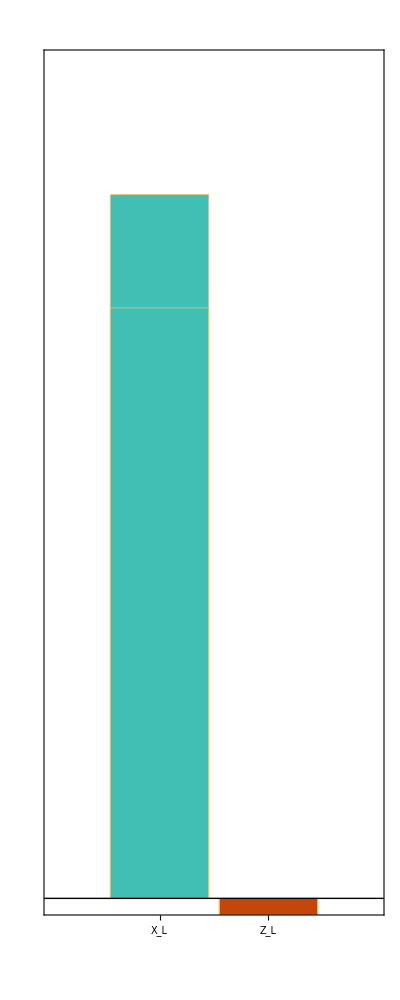

(56) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

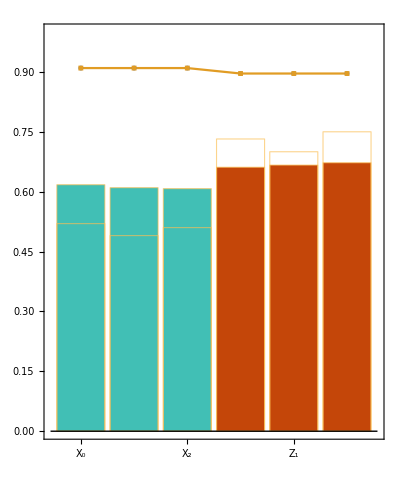
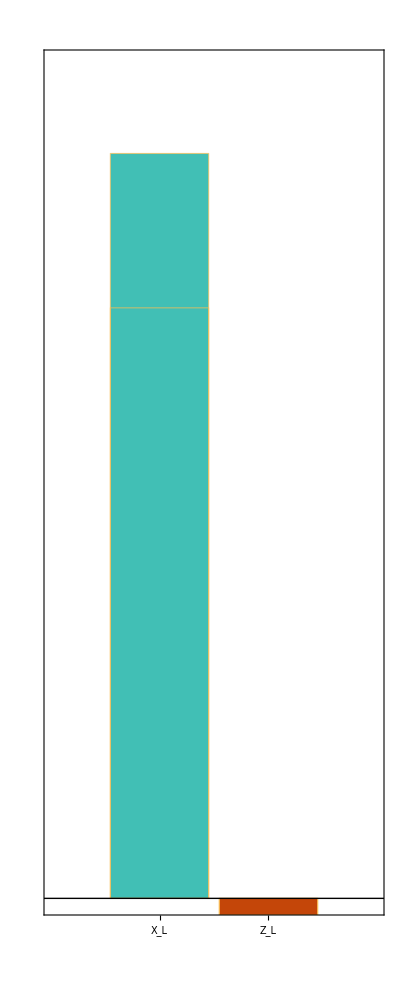

(57) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

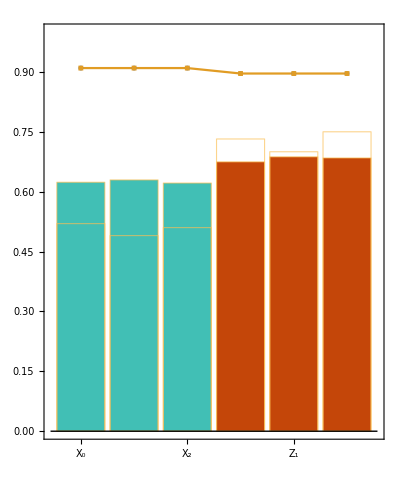
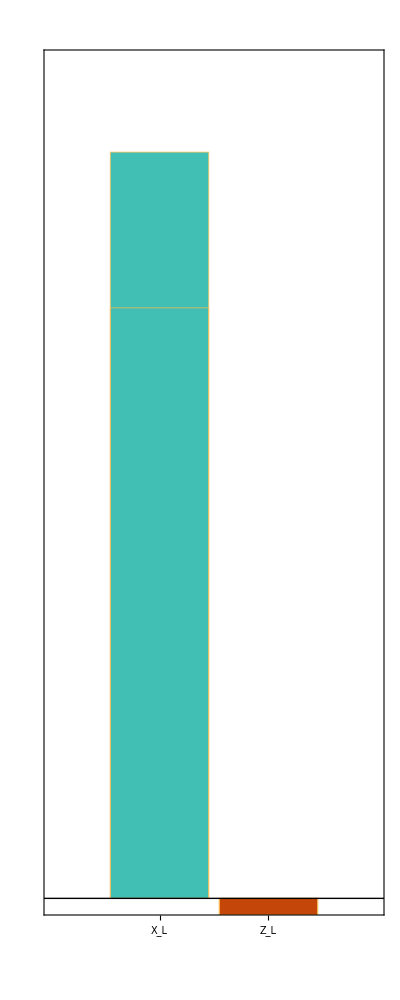

(58) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

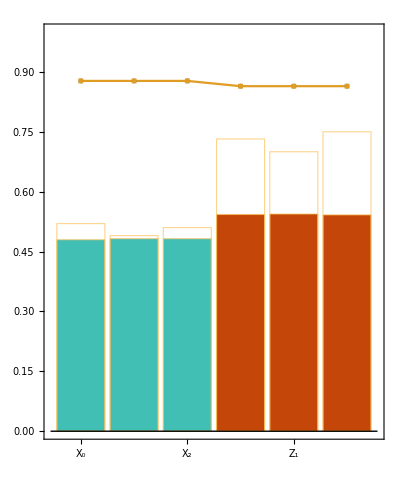
-Graphics--Graphics-

(59) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

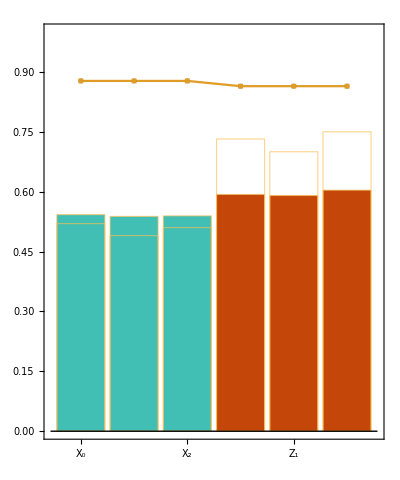
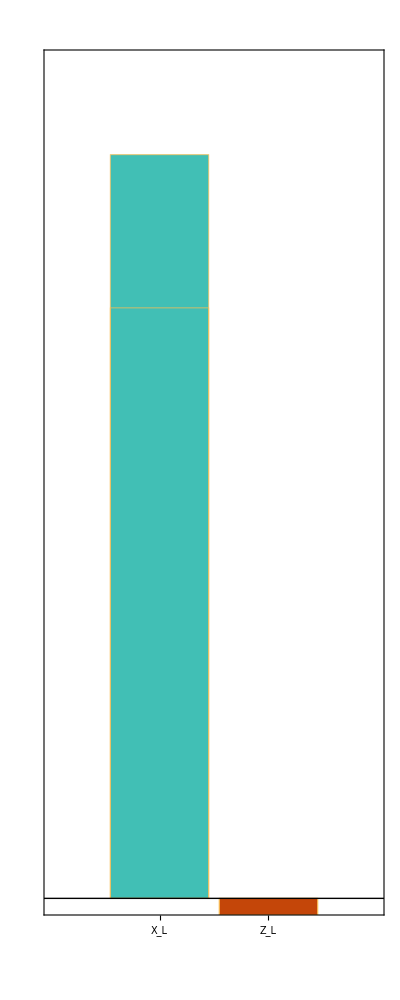

(60) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

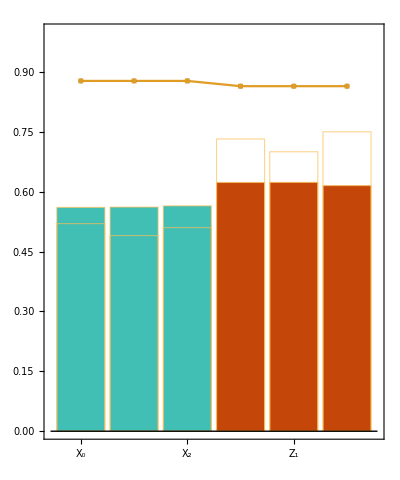
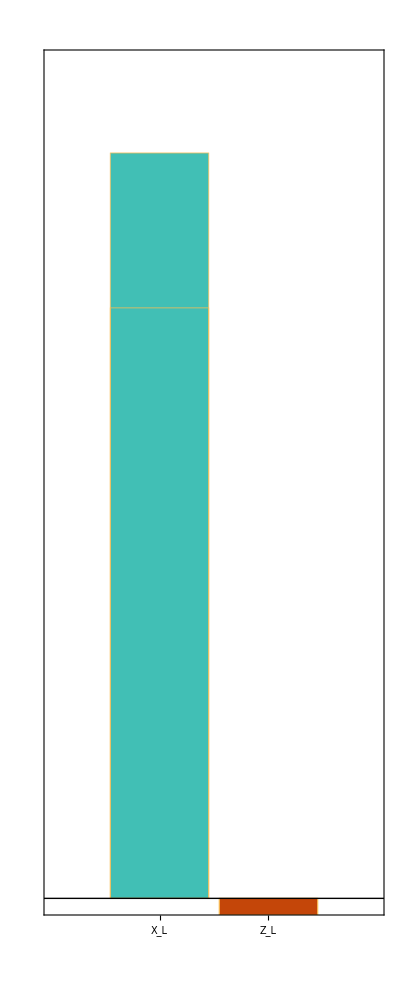

(61) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

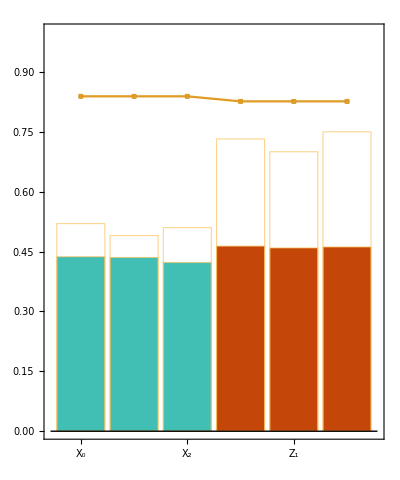
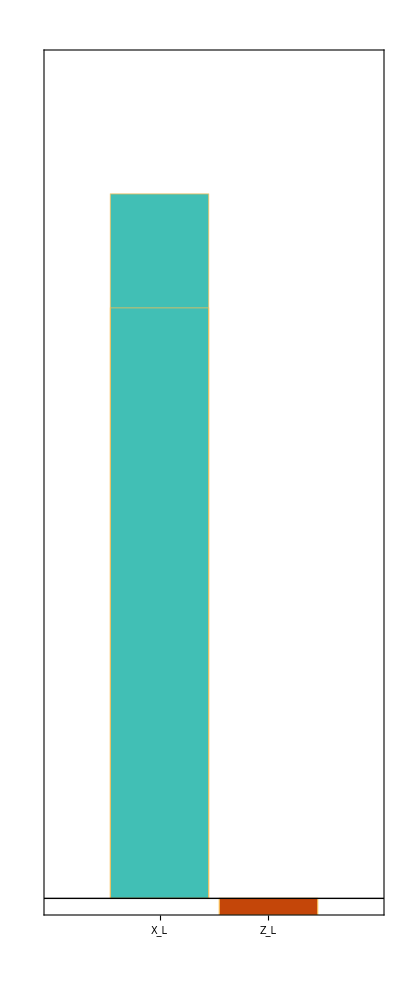

(62) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

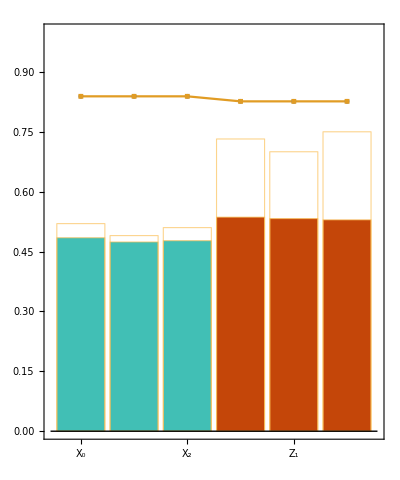
-Graphics--Graphics-

(63) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(64) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(65) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(66) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(67) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(68) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(69) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(70) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(71) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(72) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(73) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(74) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(75) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(76) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(77) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(78) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(79) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(80) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(81) opt={ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(82) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(83) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(84) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(85) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(86) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(87) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(88) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(89) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(90) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(91) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(92) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(93) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(94) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(95) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(96) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(97) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(98) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(99) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(100) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(101) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(102) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(103) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(104) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(105) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(106) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(107) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(108) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(109) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(110) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(111) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(112) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(113) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(114) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(115) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(116) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(117) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(118) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(119) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(120) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(121) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(122) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(123) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(124) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(125) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(126) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(127) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(128) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(129) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(130) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(131) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(132) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(133) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(134) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(135) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(136) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(137) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(138) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(139) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(140) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(141) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(142) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(143) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(144) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(145) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(146) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(147) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(148) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(149) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(150) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(151) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(152) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(153) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(154) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(155) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(156) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(157) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(158) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(159) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(160) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(161) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(162) opt={ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(163) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(164) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(165) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(166) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(167) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(168) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(169) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(170) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(171) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(172) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(173) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(174) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(175) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(176) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(177) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(178) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(179) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(180) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(181) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(182) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(183) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(184) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(185) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(186) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(187) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(188) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(189) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(190) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(191) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(192) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(193) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(194) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(195) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(196) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(197) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(198) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(199) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(200) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(201) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(202) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(203) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(204) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(205) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(206) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(207) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(208) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(209) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(210) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(211) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(212) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(213) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(214) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(215) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(216) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(217) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(218) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(219) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(220) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(221) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(222) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(223) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(224) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(225) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(226) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(227) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(228) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(229) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(230) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(231) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(232) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(233) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(234) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(235) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(236) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(237) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(238) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(239) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(240) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(241) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(242) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(243) opt={ProbBFRot→<|10→0.01,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(244) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(245) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(246) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(247) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(248) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(249) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(250) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(251) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(252) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(253) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(254) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(255) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(256) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(257) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(258) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(259) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(260) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(261) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(262) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(263) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(264) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(265) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(266) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(267) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(268) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(269) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(270) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(271) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(272) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(273) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(274) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(275) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(276) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(277) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(278) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(279) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(280) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(281) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(282) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(283) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(284) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(285) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(286) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(287) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(288) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(289) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(290) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(291) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(292) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(293) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(294) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(295) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(296) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(297) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(298) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(299) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(300) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(301) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(302) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(303) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(304) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(305) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(306) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(307) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(308) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(309) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(310) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(311) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(312) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(313) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(314) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(315) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(316) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(317) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(318) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(319) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(320) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(321) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(322) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(323) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(324) opt={ProbBFRot→<|10→0.01,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(325) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(326) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(327) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(328) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(329) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(330) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(331) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(332) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(333) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(334) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(335) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(336) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(337) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(338) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(339) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(340) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(341) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(342) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(343) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(344) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(345) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(346) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(347) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(348) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(349) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(350) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(351) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(352) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(353) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(354) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(355) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(356) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(357) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(358) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(359) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(360) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(361) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(362) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(363) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(364) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(365) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(366) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(367) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(368) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(369) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(370) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(371) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(372) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(373) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(374) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(375) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(376) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(377) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(378) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(379) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(380) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(381) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(382) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(383) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(384) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(385) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(386) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(387) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(388) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(389) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(390) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(391) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(392) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(393) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(394) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(395) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(396) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(397) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(398) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(399) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(400) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(401) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(402) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(403) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(404) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(405) opt={ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(406) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(407) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(408) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(409) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(410) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(411) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(412) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(413) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(414) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(415) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(416) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(417) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(418) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(419) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(420) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(421) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(422) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(423) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(424) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(425) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(426) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(427) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(428) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(429) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(430) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(431) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(432) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(433) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(434) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(435) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(436) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(437) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(438) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(439) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(440) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(441) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(442) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(443) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(444) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(445) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(446) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(447) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(448) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(449) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(450) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(451) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(452) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(453) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(454) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(455) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(456) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(457) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(458) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(459) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(460) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(461) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(462) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(463) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(464) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(465) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(466) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(467) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(468) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(469) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(470) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(471) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(472) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(473) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(474) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(475) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(476) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(477) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(478) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(479) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(480) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(481) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(482) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(483) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(484) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(485) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(486) opt={ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(487) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(488) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(489) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(490) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(491) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(492) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(493) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(494) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(495) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(496) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(497) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(498) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(499) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(500) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(501) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(502) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(503) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(504) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(505) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(506) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(507) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(508) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(509) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(510) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(511) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(512) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(513) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(514) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(515) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(516) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(517) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(518) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(519) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(520) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(521) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(522) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(523) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(524) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(525) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(526) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(527) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(528) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(529) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(530) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(531) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(532) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(533) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(534) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(535) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(536) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(537) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(538) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(539) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(540) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(541) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(542) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(543) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(544) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(545) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(546) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(547) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(548) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(549) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(550) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(551) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(552) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(553) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(554) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(555) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(556) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(557) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(558) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(559) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(560) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(561) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(562) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(563) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(564) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(565) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(566) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(567) opt={ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(568) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(569) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(570) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(571) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(572) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(573) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(574) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(575) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(576) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(577) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(578) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(579) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(580) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(581) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(582) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(583) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(584) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(585) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(586) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(587) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(588) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(589) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(590) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(591) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(592) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(593) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(594) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(595) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(596) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(597) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(598) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(599) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(600) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(601) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(602) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(603) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(604) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(605) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(606) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(607) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(608) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(609) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(610) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(611) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(612) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(613) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(614) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(615) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(616) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(617) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(618) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(619) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(620) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(621) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(622) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(623) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(624) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(625) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(626) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(627) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(628) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(629) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(630) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(631) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(632) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(633) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(634) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(635) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(636) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(637) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(638) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(639) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(640) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(641) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(642) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(643) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(644) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(645) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(646) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(647) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(648) opt={ProbBFRot→<|10→0.02,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(649) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(650) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(651) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(652) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(653) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(654) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(655) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(656) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(657) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(658) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(659) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(660) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(661) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(662) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(663) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(664) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(665) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(666) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(667) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(668) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(669) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(670) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(671) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(672) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(673) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(674) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(675) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(676) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(677) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(678) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(679) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(680) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(681) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(682) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(683) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(684) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(685) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(686) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(687) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(688) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(689) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(690) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(691) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(692) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(693) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(694) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(695) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(696) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(697) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(698) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(699) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(700) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(701) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(702) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(703) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(704) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(705) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(706) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(707) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(708) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(709) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(710) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(711) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(712) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(713) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(714) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(715) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(716) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(717) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(718) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(719) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(720) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(721) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(722) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(723) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(724) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(725) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(726) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(727) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(728) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(729) opt={ProbBFRot→<|10→0.03,1→0.02|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(730) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(731) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(732) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(733) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(734) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(735) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(736) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(737) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(738) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(739) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(740) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(741) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(742) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(743) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(744) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(745) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(746) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(747) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(748) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(749) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(750) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(751) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(752) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(753) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(754) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(755) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(756) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(757) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(758) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(759) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(760) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(761) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(762) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(763) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(764) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(765) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(766) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(767) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(768) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(769) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(770) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(771) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(772) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(773) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(774) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(775) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(776) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(777) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(778) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(779) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(780) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(781) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(782) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(783) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(784) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(785) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(786) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(787) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(788) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(789) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(790) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(791) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(792) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(793) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(794) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(795) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(796) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(797) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(798) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(799) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(800) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(801) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(802) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(803) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(804) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(805) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(806) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(807) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(808) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(809) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(810) opt={ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(811) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(812) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(813) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(814) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(815) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(816) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(817) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(818) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(819) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(820) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(821) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(822) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(823) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(824) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(825) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(826) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(827) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(828) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(829) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(830) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(831) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(832) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(833) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(834) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(835) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(836) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(837) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(838) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(839) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(840) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(841) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(842) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(843) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(844) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(845) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(846) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(847) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(848) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(849) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(850) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(851) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(852) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(853) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(854) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(855) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(856) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(857) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(858) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(859) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(860) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(861) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(862) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(863) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(864) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(865) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(866) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(867) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(868) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(869) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(870) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(871) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(872) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(873) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(874) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(875) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(876) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(877) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(878) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(879) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(880) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(881) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(882) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(883) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(884) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(885) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(886) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(887) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(888) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(889) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(890) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(891) opt={ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(892) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(893) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(894) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(895) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(896) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(897) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(898) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(899) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(900) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(901) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(902) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(903) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(904) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(905) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(906) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(907) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(908) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(909) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(910) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(911) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(912) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(913) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(914) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(915) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(916) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(917) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(918) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(919) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(920) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(921) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(922) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(923) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(924) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(925) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(926) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(927) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(928) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(929) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(930) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(931) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(932) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(933) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(934) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(935) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(936) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(937) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(938) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(939) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(940) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(941) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(942) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(943) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(944) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(945) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(946) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(947) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(948) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(949) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(950) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(951) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(952) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(953) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(954) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.006,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(955) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(956) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(957) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(958) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(959) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(960) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(961) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(962) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(963) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.01,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

(964) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96}

-Graphics--Graphics-

(965) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(966) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

-Graphics--Graphics-

(967) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96}

-Graphics--Graphics-

(968) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.977}

-Graphics--Graphics-

(969) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

-Graphics--Graphics-

(970) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.96}

-Graphics--Graphics-

(971) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(972) opt={ProbBFRot→<|10→0.03,1→0.05|>,ProbLeakInit→0.005,ProbLeakCZ→<|10→0.05,11→0.01|>,FidMeas→0.98}

-Graphics--Graphics-

```mathematica
steaneCharts[#,stabsteane,logsteane]&/@steane7
```

## Simulation on steane 2

```mathematica
fbrot=Flatten@Table[<|10->i,01->j|>,{i,{0.001,0.005}},{j,{0.01,0.001}}];
probleakinit={0.001,0.005};
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.001}},{j,{0.0001}}];
fidmeas={0.977,0.975}
```

{0.977,0.975}

```mathematica
options=Flatten[Table[{{ProbBFRot->i,FidMeas->0.977},{ProbLeakInit->j,FidMeas->0.977},{ProbLeakCZ->k,FidMeas->0.977}},{i,fbrot},{j,probleakinit},{k,probleakcz}],3];
Length@options
```

96

### Run two

```mathematica
idx=1;
nshots=10000;
Table[
Print["(",idx++,") opt=",opt];
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,opt];
AppendTo[steane7,res];
DumpSave["steane7.mx",steane7];
,{opt,options}];
```

(1) opt={ProbBFRot→<|10→0.001,1→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(2) opt={ProbLeakInit→0.001,FidMeas→0.977}

-Graphics--Graphics-

(3) opt={ProbLeakCZ→<|10→0.001,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(4) opt={ProbBFRot→<|10→0.001,1→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(5) opt={ProbLeakInit→0.005,FidMeas→0.977}

-Graphics--Graphics-

(6) opt={ProbLeakCZ→<|10→0.001,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(7) opt={ProbBFRot→<|10→0.001,1→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(8) opt={ProbLeakInit→0.001,FidMeas→0.977}

-Graphics--Graphics-

(9) opt={ProbLeakCZ→<|10→0.001,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(10) opt={ProbBFRot→<|10→0.001,1→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(11) opt={ProbLeakInit→0.005,FidMeas→0.977}

-Graphics--Graphics-

(12) opt={ProbLeakCZ→<|10→0.001,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(13) opt={ProbBFRot→<|10→0.005,1→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(14) opt={ProbLeakInit→0.001,FidMeas→0.977}

-Graphics--Graphics-

(15) opt={ProbLeakCZ→<|10→0.001,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(16) opt={ProbBFRot→<|10→0.005,1→0.01|>,FidMeas→0.977}

-Graphics--Graphics-

(17) opt={ProbLeakInit→0.005,FidMeas→0.977}

-Graphics--Graphics-

(18) opt={ProbLeakCZ→<|10→0.001,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(19) opt={ProbBFRot→<|10→0.005,1→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(20) opt={ProbLeakInit→0.001,FidMeas→0.977}

-Graphics--Graphics-

(21) opt={ProbLeakCZ→<|10→0.001,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(22) opt={ProbBFRot→<|10→0.005,1→0.001|>,FidMeas→0.977}

-Graphics--Graphics-

(23) opt={ProbLeakInit→0.005,FidMeas→0.977}

-Graphics--Graphics-

(24) opt={ProbLeakCZ→<|10→0.001,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

### Run three: manual adjustment of error parameters

```mathematica
DestroyAllQuregs[]
{ρ,ρinit,ρwork,ρstore}=CreateDensityQuregs[7,4];
SetQuregMatrix[ρinit,RandomMixState[7]];
```

```mathematica
steane7<<steane7.mx;
```

```mathematica
steane7//Length
```

1047

```mathematica
fbrot=Flatten@Table[<|10->i,01->j|>,{i,{0.0001,0.002}},{j,{0.11,0.12}}];
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.01,0.02}},{j,{0.0001,0.0002}}];
fidmeas={0.975,0.977};
options=Flatten[Table[{ProbBFRot->i,ProbLeakInit->0.00001,ProbLeakCZ->k,FidMeas->l},{i,fbrot},{k,probleakcz},{l,fidmeas}],2];
Length@options
```

32

```mathematica
nshots=10000;
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,{ProbLeakInit->0.00002,ProbBFRot-><|10->0.0005,01->0.15|>,ProbLeakCZ-><|10->0.01,11->0.0002|>,FidMeas->0.97,ProbLeakMove->0.0005}];
AppendTo[steane7,res];
DumpSave["steane7.mx",steane7];
```

-Graphics--Graphics-

```mathematica
`
```

```mathematica
nshots=10000;
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,{ProbLeakInit->0.00001,ProbBFRot-><|10->0.0001,01->0.11|>,ProbLeakCZ-><|10->0.01,11->0.0002|>,FidMeas->0.97,ProbLeakMove->0.0003}];
AppendTo[steane7,res];
DumpSave["steane7.mx",steane7];
```

(0) opt={ProbBFRot→<|10→0.01,1→0.0001|>,ProbLeakCZ→<|10→0.001,11→0.0001|>,FidMeas→0.98,ProbLeakMove→0.005,ProbLeakInit→0.02}

-Graphics--Graphics-

```mathematica
idx=1;
nshots=10000;
Table[
Print["(",idx++,") opt=",opt];
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,opt];
AppendTo[steane7,res];
DumpSave["steane7.mx",steane7];
,{opt,options}];
```

(1) opt={ProbBFRot→<|10→0.0001,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0001|>,FidMeas→0.975}

-Graphics--Graphics-

(2) opt={ProbBFRot→<|10→0.0001,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(3) opt={ProbBFRot→<|10→0.0001,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0002|>,FidMeas→0.975}

-Graphics--Graphics-

(4) opt={ProbBFRot→<|10→0.0001,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0002|>,FidMeas→0.977}

-Graphics--Graphics-

(5) opt={ProbBFRot→<|10→0.0001,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0001|>,FidMeas→0.975}

-Graphics--Graphics-

(6) opt={ProbBFRot→<|10→0.0001,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(7) opt={ProbBFRot→<|10→0.0001,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0002|>,FidMeas→0.975}

-Graphics--Graphics-

(8) opt={ProbBFRot→<|10→0.0001,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0002|>,FidMeas→0.977}

-Graphics--Graphics-

(9) opt={ProbBFRot→<|10→0.0001,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0001|>,FidMeas→0.975}

-Graphics--Graphics-

(10) opt={ProbBFRot→<|10→0.0001,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(11) opt={ProbBFRot→<|10→0.0001,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0002|>,FidMeas→0.975}

-Graphics--Graphics-

(12) opt={ProbBFRot→<|10→0.0001,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0002|>,FidMeas→0.977}

-Graphics--Graphics-

(13) opt={ProbBFRot→<|10→0.0001,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0001|>,FidMeas→0.975}

-Graphics--Graphics-

(14) opt={ProbBFRot→<|10→0.0001,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(15) opt={ProbBFRot→<|10→0.0001,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0002|>,FidMeas→0.975}

-Graphics--Graphics-

(16) opt={ProbBFRot→<|10→0.0001,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0002|>,FidMeas→0.977}

-Graphics--Graphics-

(17) opt={ProbBFRot→<|10→0.002,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0001|>,FidMeas→0.975}

-Graphics--Graphics-

(18) opt={ProbBFRot→<|10→0.002,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(19) opt={ProbBFRot→<|10→0.002,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0002|>,FidMeas→0.975}

-Graphics--Graphics-

(20) opt={ProbBFRot→<|10→0.002,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0002|>,FidMeas→0.977}

-Graphics--Graphics-

(21) opt={ProbBFRot→<|10→0.002,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0001|>,FidMeas→0.975}

-Graphics--Graphics-

(22) opt={ProbBFRot→<|10→0.002,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(23) opt={ProbBFRot→<|10→0.002,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0002|>,FidMeas→0.975}

-Graphics--Graphics-

(24) opt={ProbBFRot→<|10→0.002,1→0.11|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0002|>,FidMeas→0.977}

-Graphics--Graphics-

(25) opt={ProbBFRot→<|10→0.002,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0001|>,FidMeas→0.975}

-Graphics--Graphics-

(26) opt={ProbBFRot→<|10→0.002,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(27) opt={ProbBFRot→<|10→0.002,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0002|>,FidMeas→0.975}

-Graphics--Graphics-

(28) opt={ProbBFRot→<|10→0.002,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.01,11→0.0002|>,FidMeas→0.977}

-Graphics--Graphics-

(29) opt={ProbBFRot→<|10→0.002,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0001|>,FidMeas→0.975}

-Graphics--Graphics-

(30) opt={ProbBFRot→<|10→0.002,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0001|>,FidMeas→0.977}

-Graphics--Graphics-

(31) opt={ProbBFRot→<|10→0.002,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0002|>,FidMeas→0.975}

-Graphics--Graphics-

(32) opt={ProbBFRot→<|10→0.002,1→0.12|>,ProbLeakInit→0.00001,ProbLeakCZ→<|10→0.02,11→0.0002|>,FidMeas→0.977}

-Graphics--Graphics-

## Results

```mathematica
steane7<<steane7.mx
```

Null steane7

```mathematica
stabsteane={{0.52,0.49,0.51},{0.732,0.7,0.75}};
logsteane={0.71,-0.02};
```

```mathematica
steaneres=steaneResults[#,stabsteane,logsteane]&/@steane7;
```

```mathematica
steaneres[[1]]//Keys
```

{nshots,charts,avgstab,errmaxstab,erravgstab,errlogic,idealavg}

```mathematica
Ordering[Total/@Values@steaneres[[All,"errmaxstab"]],1]
Ordering[Total/@Values@steaneres[[All,"erravgstab"]],1]
Ordering[Total/@Values@steaneres[[All,"errlogic"]],1]
```

{1012}

{1012}

{1006}

```mathematica
steaneResults[steane7[[1008]],stabsteane,logsteane]
```

<|nshots→10000,charts→-Graphics--Graphics-,avgstab→<|x→0.500733,z→0.7148,xl→0.749,zl→-0.0136|>,errmaxstab→<|x→0.0216,z→0.041|>,erravgstab→<|x→0.0132667,z→0.0246667|>,errlogic→<|x→0.039,z→0.0064|>,idealavg→<|x→0.790098,z→0.837149,xl→0.837427,zl→0.000037635|>|>

```mathematica
steaneres[[{1007,1008,1015}]]
```

{<|nshots→10000,charts→-Graphics--Graphics-,avgstab→<|x→0.5174,z→0.7178,xl→0.7518,zl→-0.0174|>,errmaxstab→<|x→0.0362,z→0.0372|>,erravgstab→<|x→0.0134,z→0.0255333|>,errlogic→<|x→0.0418,z→0.0026|>,idealavg→<|x→0.807969,z→0.851363,xl→0.851599,zl→0.0000242311|>|>,<|nshots→10000,charts→-Graphics--Graphics-,avgstab→<|x→0.500733,z→0.7148,xl→0.749,zl→-0.0136|>,errmaxstab→<|x→0.0216,z→0.041|>,erravgstab→<|x→0.0132667,z→0.0246667|>,errlogic→<|x→0.039,z→0.0064|>,idealavg→<|x→0.790098,z→0.837149,xl→0.837427,zl→0.000037635|>|>,<|nshots→10000,charts→-Graphics--Graphics-,avgstab→<|x→0.483467,z→0.704667,xl→0.7488,zl→-0.0186|>,errmaxstab→<|x→0.045,z→0.0498|>,erravgstab→<|x→0.0232,z→0.0308|>,errlogic→<|x→0.0388,z→0.0014|>,idealavg→<|x→0.788994,z→0.83598,xl→0.83622,zl→0.0000395572|>|>}

```mathematica
steaneres[[1008]]
```

<|nshots→10000,charts→-Graphics--Graphics-,errmaxstab→<|x→0.0216,z→0.041|>,erravgstab→<|x→<|0→0.0138667,1→0.013,2→0.0124|>,z→<|0→0.0243333,1→0.0212667,2→0.0216|>|>,errlogic→<|x→0.039,z→0.0064|>,idealavg→<|x→0.790098,z→0.837149,xl→0.837427,zl→0.000037635|>|>